```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}];
```

/home/zack/cantera/ratematrix

## Random matrices

data/random2

{996,5,0.00682633}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

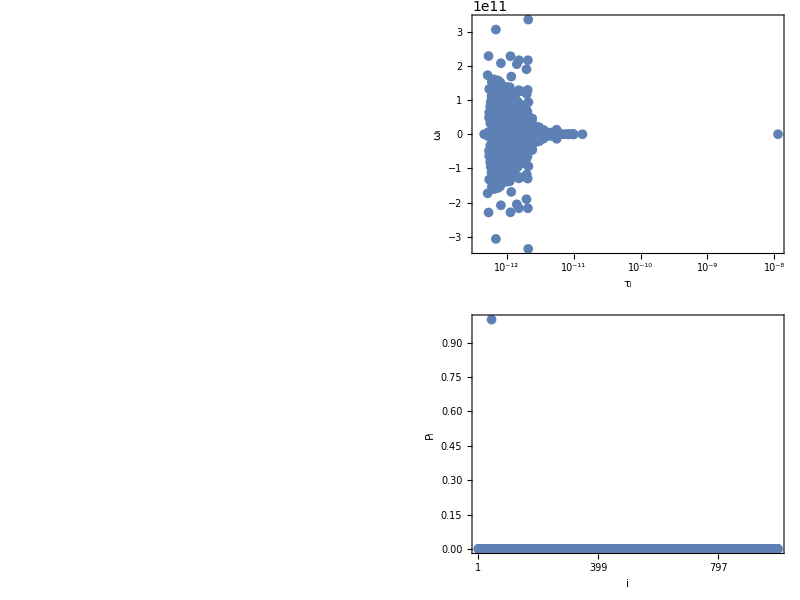

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
A=SparseArray[Table[{columns[[i]]+1,rows[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Transition matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}},MaxPlotPoints->200]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
```

data/random2

{996,5,0.00682633}

28.459

{12.3703,Null}

8.62557×10^11

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

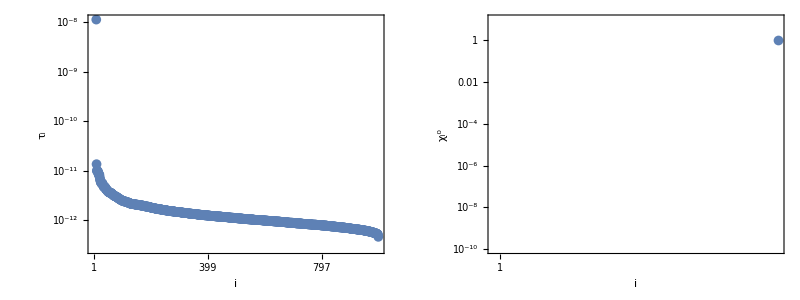

fig3.pdf

0.880026

```mathematica
filebase="data/random2"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
AbsoluteTiming[angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];]
max=Pi/2;
r=1;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A],ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},MaxPlotPoints->200]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.88}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.88}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig3.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

```mathematica
Count[Eigenvalues[A+Transpose[A]],u_/;Re[u]>=0]
Count[Eigenvalues[A],u_/;Re[u]>=0]
```

Eigenvalues::arh: Because finding 996 out of the 996 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

11

Eigenvalues::arh: Because finding 996 out of the 996 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

9

```mathematica
evals
```

{-2.18574×10^12+0. ⅈ,-2.01434×10^12+0. ⅈ,-1.93673×10^12-1.72848×10^11 ⅈ,-1.93673×10^12+1.72848×10^11 ⅈ,-1.90505×10^12-5.8051×10^9 ⅈ,-1.90505×10^12+5.8051×10^9 ⅈ,-1.8758×10^12-2.28982×10^11 ⅈ,-1.8758×10^12+2.28982×10^11 ⅈ,-1.85634×10^12-3.83419×10^9 ⅈ,-1.85634×10^12+3.83419×10^9 ⅈ,-1.85058×10^12-4.84938×10^10 ⅈ,-1.85058×10^12+4.84938×10^10 ⅈ,-1.83499×10^12-1.3254×10^11 ⅈ,-1.83499×10^12+1.3254×10^11 ⅈ,-1.83399×10^12-6.35247×10^10 ⅈ,-1.83399×10^12+6.35247×10^10 ⅈ,-1.80827×10^12+0. ⅈ,-1.79234×10^12+0. ⅈ,-1.773×10^12-8.0743×10^10 ⅈ,-1.773×10^12+8.0743×10^10 ⅈ,-1.76809×10^12-3.24726×10^10 ⅈ,-1.76809×10^12+3.24726×10^10 ⅈ,-1.75297×10^12+0. ⅈ,-1.75055×10^12-6.31711×10^10 ⅈ,-1.75055×10^12+6.31711×10^10 ⅈ,-1.74216×10^12-9.50079×10^10 ⅈ,-1.74216×10^12+9.50079×10^10 ⅈ,-1.72836×10^12+0. ⅈ,-1.71947×10^12-7.32391×10^10 ⅈ,-1.71947×10^12+7.32391×10^10 ⅈ,-1.69804×10^12-5.32606×10^10 ⅈ,-1.69804×10^12+5.32606×10^10 ⅈ,-1.69579×10^12-4.04818×10^10 ⅈ,-1.69579×10^12+4.04818×10^10 ⅈ,-1.69575×10^12-1.11699×10^11 ⅈ,-1.69575×10^12+1.11699×10^11 ⅈ,-1.67659×10^12-1.53134×10^11 ⅈ,-1.67659×10^12+1.53134×10^11 ⅈ,-1.65991×10^12-5.81673×10^10 ⅈ,-1.65991×10^12+5.81673×10^10 ⅈ,-1.65372×10^12-1.09648×10^10 ⅈ,-1.65372×10^12+1.09648×10^10 ⅈ,-1.64828×10^12-9.55813×10^10 ⅈ,-1.64828×10^12+9.55813×10^10 ⅈ,-1.64089×10^12-3.14236×10^10 ⅈ,-1.64089×10^12+3.14236×10^10 ⅈ,-1.63556×10^12-1.29083×10^11 ⅈ,-1.63556×10^12+1.29083×10^11 ⅈ,-1.63478×10^12-1.02594×10^11 ⅈ,-1.63478×10^12+1.02594×10^11 ⅈ,-1.61655×10^12-7.49401×10^10 ⅈ,-1.61655×10^12+7.49401×10^10 ⅈ,-1.61417×10^12+0. ⅈ,-1.60489×10^12-1.50388×10^11 ⅈ,-1.60489×10^12+1.50388×10^11 ⅈ,-1.59945×10^12+0. ⅈ,-1.59793×10^12-6.69264×10^10 ⅈ,-1.59793×10^12+6.69264×10^10 ⅈ,-1.59791×10^12-3.05633×10^10 ⅈ,-1.59791×10^12+3.05633×10^10 ⅈ,-1.59016×10^12-2.68997×10^10 ⅈ,-1.59016×10^12+2.68997×10^10 ⅈ,-1.58941×10^12-4.97014×10^10 ⅈ,-1.58941×10^12+4.97014×10^10 ⅈ,-1.58021×10^12+0. ⅈ,-1.5642×10^12-7.46264×10^10 ⅈ,-1.5642×10^12+7.46264×10^10 ⅈ,-1.55834×10^12-1.18592×10^11 ⅈ,-1.55834×10^12+1.18592×10^11 ⅈ,-1.55716×10^12+0. ⅈ,-1.55604×10^12-1.60664×10^11 ⅈ,-1.55604×10^12+1.60664×10^11 ⅈ,-1.55129×10^12-3.19512×10^10 ⅈ,-1.55129×10^12+3.19512×10^10 ⅈ,-1.5434×10^12+0. ⅈ,-1.54195×10^12-3.13814×10^10 ⅈ,-1.54195×10^12+3.13814×10^10 ⅈ,-1.5403×10^12+0. ⅈ,-1.53638×10^12-1.00782×10^11 ⅈ,-1.53638×10^12+1.00782×10^11 ⅈ,-1.52117×10^12-4.13133×10^10 ⅈ,-1.52117×10^12+4.13133×10^10 ⅈ,-1.51463×10^12+0. ⅈ,-1.51387×10^12-1.19521×10^11 ⅈ,-1.51387×10^12+1.19521×10^11 ⅈ,-1.51314×10^12-1.0098×10^11 ⅈ,-1.51314×10^12+1.0098×10^11 ⅈ,-1.5122×10^12-1.43748×10^10 ⅈ,-1.5122×10^12+1.43748×10^10 ⅈ,-1.50603×10^12-7.86598×10^10 ⅈ,-1.50603×10^12+7.86598×10^10 ⅈ,-1.49679×10^12-1.38447×10^11 ⅈ,-1.49679×10^12+1.38447×10^11 ⅈ,-1.49676×10^12+0. ⅈ,-1.4906×10^12-4.81467×10^10 ⅈ,-1.4906×10^12+4.81467×10^10 ⅈ,-1.48945×10^12-2.09258×10^10 ⅈ,-1.48945×10^12+2.09258×10^10 ⅈ,-1.48103×10^12-7.46917×10^10 ⅈ,-1.48103×10^12+7.46917×10^10 ⅈ,-1.47186×10^12-4.70661×10^10 ⅈ,-1.47186×10^12+4.70661×10^10 ⅈ,-1.46343×10^12-3.0324×10^9 ⅈ,-1.46343×10^12+3.0324×10^9 ⅈ,-1.46094×10^12-8.59607×10^10 ⅈ,-1.46094×10^12+8.59607×10^10 ⅈ,-1.45949×10^12-2.54172×10^10 ⅈ,-1.45949×10^12+2.54172×10^10 ⅈ,-1.45897×10^12-3.06417×10^11 ⅈ,-1.45897×10^12+3.06417×10^11 ⅈ,-1.44684×10^12-1.83683×10^10 ⅈ,-1.44684×10^12+1.83683×10^10 ⅈ,-1.44528×10^12-8.51825×10^10 ⅈ,-1.44528×10^12+8.51825×10^10 ⅈ,-1.44279×10^12+0. ⅈ,-1.43457×10^12-1.39365×10^11 ⅈ,-1.43457×10^12+1.39365×10^11 ⅈ,-1.4228×10^12-2.79025×10^10 ⅈ,-1.4228×10^12+2.79025×10^10 ⅈ,-1.4217×10^12-1.05346×10^11 ⅈ,-1.4217×10^12+1.05346×10^11 ⅈ,-1.42014×10^12-4.54209×10^10 ⅈ,-1.42014×10^12+4.54209×10^10 ⅈ,-1.41873×10^12+0. ⅈ,-1.41787×10^12+0. ⅈ,-1.41341×10^12-7.65857×10^10 ⅈ,-1.41341×10^12+7.65857×10^10 ⅈ,-1.4113×10^12-1.29093×10^11 ⅈ,-1.4113×10^12+1.29093×10^11 ⅈ,-1.40543×10^12-3.79107×10^10 ⅈ,-1.40543×10^12+3.79107×10^10 ⅈ,-1.40349×10^12-2.05416×10^10 ⅈ,-1.40349×10^12+2.05416×10^10 ⅈ,-1.40081×10^12-7.47549×10^10 ⅈ,-1.40081×10^12+7.47549×10^10 ⅈ,-1.39894×10^12-3.96267×10^9 ⅈ,-1.39894×10^12+3.96267×10^9 ⅈ,-1.39863×10^12-1.02592×10^11 ⅈ,-1.39863×10^12+1.02592×10^11 ⅈ,-1.39054×10^12-1.51733×10^10 ⅈ,-1.39054×10^12+1.51733×10^10 ⅈ,-1.37832×10^12-5.8054×10^10 ⅈ,-1.37832×10^12+5.8054×10^10 ⅈ,-1.37527×10^12-3.87162×10^10 ⅈ,-1.37527×10^12+3.87162×10^10 ⅈ,-1.37461×10^12+0. ⅈ,-1.36961×10^12-2.48434×10^10 ⅈ,-1.36961×10^12+2.48434×10^10 ⅈ,-1.3634×10^12-1.49436×10^10 ⅈ,-1.3634×10^12+1.49436×10^10 ⅈ,-1.36252×10^12-1.57528×10^11 ⅈ,-1.36252×10^12+1.57528×10^11 ⅈ,-1.3571×10^12-1.31459×10^11 ⅈ,-1.3571×10^12+1.31459×10^11 ⅈ,-1.35322×10^12-8.73955×10^10 ⅈ,-1.35322×10^12+8.73955×10^10 ⅈ,-1.35085×10^12+0. ⅈ,-1.34907×10^12-5.75762×10^10 ⅈ,-1.34907×10^12+5.75762×10^10 ⅈ,-1.34595×10^12-1.97185×10^10 ⅈ,-1.34595×10^12+1.97185×10^10 ⅈ,-1.34456×10^12-6.95896×10^10 ⅈ,-1.34456×10^12+6.95896×10^10 ⅈ,-1.34072×10^12-4.07935×10^10 ⅈ,-1.34072×10^12+4.07935×10^10 ⅈ,-1.33823×10^12-2.58392×10^10 ⅈ,-1.33823×10^12+2.58392×10^10 ⅈ,-1.3346×10^12-1.05896×10^11 ⅈ,-1.3346×10^12+1.05896×10^11 ⅈ,-1.33276×10^12+0. ⅈ,-1.32503×10^12+0. ⅈ,-1.32195×10^12-1.295×10^10 ⅈ,-1.32195×10^12+1.295×10^10 ⅈ,-1.31632×10^12-7.40231×10^10 ⅈ,-1.31632×10^12+7.40231×10^10 ⅈ,-1.31484×10^12-4.92583×10^10 ⅈ,-1.31484×10^12+4.92583×10^10 ⅈ,-1.31346×10^12+0. ⅈ,-1.30684×10^12+0. ⅈ,-1.30614×10^12-1.2457×10^11 ⅈ,-1.30614×10^12+1.2457×10^11 ⅈ,-1.29584×10^12-7.49475×10^10 ⅈ,-1.29584×10^12+7.49475×10^10 ⅈ,-1.29493×10^12-3.06623×10^10 ⅈ,-1.29493×10^12+3.06623×10^10 ⅈ,-1.29488×10^12-4.09393×10^10 ⅈ,-1.29488×10^12+4.09393×10^10 ⅈ,-1.29307×10^12-1.28142×10^11 ⅈ,-1.29307×10^12+1.28142×10^11 ⅈ,-1.29183×10^12-1.22013×10^10 ⅈ,-1.29183×10^12+1.22013×10^10 ⅈ,-1.29182×10^12+0. ⅈ,-1.28516×10^12-9.40808×10^10 ⅈ,-1.28516×10^12+9.40808×10^10 ⅈ,-1.28471×10^12+0. ⅈ,-1.28331×10^12+0. ⅈ,-1.28242×10^12-4.32727×10^10 ⅈ,-1.28242×10^12+4.32727×10^10 ⅈ,-1.27824×10^12-6.87116×10^10 ⅈ,-1.27824×10^12+6.87116×10^10 ⅈ,-1.27746×10^12-8.24131×10^10 ⅈ,-1.27746×10^12+8.24131×10^10 ⅈ,-1.27585×10^12-1.53354×10^11 ⅈ,-1.27585×10^12+1.53354×10^11 ⅈ,-1.26662×10^12-3.74082×10^10 ⅈ,-1.26662×10^12+3.74082×10^10 ⅈ,-1.26534×10^12+0. ⅈ,-1.26084×10^12-5.83752×10^10 ⅈ,-1.26084×10^12+5.83752×10^10 ⅈ,-1.26051×10^12+0. ⅈ,-1.26022×10^12-1.45293×10^10 ⅈ,-1.26022×10^12+1.45293×10^10 ⅈ,-1.25469×10^12-2.29854×10^10 ⅈ,-1.25469×10^12+2.29854×10^10 ⅈ,-1.24849×10^12-8.08168×10^10 ⅈ,-1.24849×10^12+8.08168×10^10 ⅈ,-1.24617×10^12-9.19396×10^10 ⅈ,-1.24617×10^12+9.19396×10^10 ⅈ,-1.24296×10^12-5.0972×10^10 ⅈ,-1.24296×10^12+5.0972×10^10 ⅈ,-1.24188×10^12-1.49752×10^11 ⅈ,-1.24188×10^12+1.49752×10^11 ⅈ,-1.24087×10^12-1.02001×10^10 ⅈ,-1.24087×10^12+1.02001×10^10 ⅈ,-1.24086×10^12-3.79159×10^10 ⅈ,-1.24086×10^12+3.79159×10^10 ⅈ,-1.24079×10^12-2.09151×10^10 ⅈ,-1.24079×10^12+2.09151×10^10 ⅈ,-1.23713×10^12+0. ⅈ,-1.23535×10^12-1.14408×10^11 ⅈ,-1.23535×10^12+1.14408×10^11 ⅈ,-1.23362×10^12-1.33435×10^11 ⅈ,-1.23362×10^12+1.33435×10^11 ⅈ,-1.22838×10^12-3.25382×10^10 ⅈ,-1.22838×10^12+3.25382×10^10 ⅈ,-1.22574×10^12-2.07982×10^11 ⅈ,-1.22574×10^12+2.07982×10^11 ⅈ,-1.22462×10^12-9.37512×10^10 ⅈ,-1.22462×10^12+9.37512×10^10 ⅈ,-1.22373×10^12-6.00398×10^10 ⅈ,-1.22373×10^12+6.00398×10^10 ⅈ,-1.21812×10^12-2.9846×10^10 ⅈ,-1.21812×10^12+2.9846×10^10 ⅈ,-1.21785×10^12-4.63426×10^9 ⅈ,-1.21785×10^12+4.63426×10^9 ⅈ,-1.21751×10^12-1.56487×10^10 ⅈ,-1.21751×10^12+1.56487×10^10 ⅈ,-1.21448×10^12-5.6615×10^10 ⅈ,-1.21448×10^12+5.6615×10^10 ⅈ,-1.21038×10^12+0. ⅈ,-1.2069×10^12-6.56086×10^10 ⅈ,-1.2069×10^12+6.56086×10^10 ⅈ,-1.20667×10^12-3.6928×10^10 ⅈ,-1.20667×10^12+3.6928×10^10 ⅈ,-1.20074×10^12+0. ⅈ,-1.19815×10^12-8.67556×10^10 ⅈ,-1.19815×10^12+8.67556×10^10 ⅈ,-1.19599×10^12-3.57302×10^10 ⅈ,-1.19599×10^12+3.57302×10^10 ⅈ,-1.1957×10^12-2.88382×10^9 ⅈ,-1.1957×10^12+2.88382×10^9 ⅈ,-1.19131×10^12-5.35907×10^10 ⅈ,-1.19131×10^12+5.35907×10^10 ⅈ,-1.19019×10^12-9.12749×10^10 ⅈ,-1.19019×10^12+9.12749×10^10 ⅈ,-1.18833×10^12-1.36662×10^10 ⅈ,-1.18833×10^12+1.36662×10^10 ⅈ,-1.18235×10^12-5.81695×10^10 ⅈ,-1.18235×10^12+5.81695×10^10 ⅈ,-1.17864×10^12-4.04307×10^9 ⅈ,-1.17864×10^12+4.04307×10^9 ⅈ,-1.17829×10^12-4.3161×10^10 ⅈ,-1.17829×10^12+4.3161×10^10 ⅈ,-1.17275×10^12+0. ⅈ,-1.17185×10^12-5.65807×10^10 ⅈ,-1.17185×10^12+5.65807×10^10 ⅈ,-1.16899×10^12-1.18251×10^11 ⅈ,-1.16899×10^12+1.18251×10^11 ⅈ,-1.1689×10^12-1.409×10^11 ⅈ,-1.1689×10^12+1.409×10^11 ⅈ,-1.16871×10^12-1.91602×10^10 ⅈ,-1.16871×10^12+1.91602×10^10 ⅈ,-1.16732×10^12-3.87111×10^10 ⅈ,-1.16732×10^12+3.87111×10^10 ⅈ,-1.16514×10^12-8.57143×10^10 ⅈ,-1.16514×10^12+8.57143×10^10 ⅈ,-1.16279×10^12-9.78076×10^9 ⅈ,-1.16279×10^12+9.78076×10^9 ⅈ,-1.16124×10^12-1.46341×10^10 ⅈ,-1.16124×10^12+1.46341×10^10 ⅈ,-1.15772×10^12+0. ⅈ,-1.15505×10^12-7.42602×10^10 ⅈ,-1.15505×10^12+7.42602×10^10 ⅈ,-1.1536×10^12-4.96852×10^10 ⅈ,-1.1536×10^12+4.96852×10^10 ⅈ,-1.14952×10^12-2.41931×10^10 ⅈ,-1.14952×10^12+2.41931×10^10 ⅈ,-1.13807×10^12-8.70599×10^10 ⅈ,-1.13807×10^12+8.70599×10^10 ⅈ,-1.13532×10^12-9.76721×10^10 ⅈ,-1.13532×10^12+9.76721×10^10 ⅈ,-1.13466×10^12-6.5858×10^10 ⅈ,-1.13466×10^12+6.5858×10^10 ⅈ,-1.13423×10^12-2.77144×10^10 ⅈ,-1.13423×10^12+2.77144×10^10 ⅈ,-1.13414×10^12+0. ⅈ,-1.13222×10^12-1.72697×10^10 ⅈ,-1.13222×10^12+1.72697×10^10 ⅈ,-1.13195×10^12-8.15062×10^9 ⅈ,-1.13195×10^12+8.15062×10^9 ⅈ,-1.13175×10^12-5.21082×10^10 ⅈ,-1.13175×10^12+5.21082×10^10 ⅈ,-1.12931×10^12-1.30024×10^11 ⅈ,-1.12931×10^12+1.30024×10^11 ⅈ,-1.12291×10^12-1.00897×10^11 ⅈ,-1.12291×10^12+1.00897×10^11 ⅈ,-1.12097×10^12-3.41105×10^10 ⅈ,-1.12097×10^12+3.41105×10^10 ⅈ,-1.11803×10^12-1.08911×10^10 ⅈ,-1.11803×10^12+1.08911×10^10 ⅈ,-1.1121×10^12-4.17983×10^10 ⅈ,-1.1121×10^12+4.17983×10^10 ⅈ,-1.11168×10^12-6.38899×10^10 ⅈ,-1.11168×10^12+6.38899×10^10 ⅈ,-1.11107×10^12-1.46743×10^10 ⅈ,-1.11107×10^12+1.46743×10^10 ⅈ,-1.10499×10^12-1.15632×10^11 ⅈ,-1.10499×10^12+1.15632×10^11 ⅈ,-1.10185×10^12-3.9718×10^10 ⅈ,-1.10185×10^12+3.9718×10^10 ⅈ,-1.10129×10^12-1.83537×10^9 ⅈ,-1.10129×10^12+1.83537×10^9 ⅈ,-1.09915×10^12-6.0994×10^10 ⅈ,-1.09915×10^12+6.0994×10^10 ⅈ,-1.09861×10^12-1.96085×10^10 ⅈ,-1.09861×10^12+1.96085×10^10 ⅈ,-1.09554×10^12-7.65502×10^10 ⅈ,-1.09554×10^12+7.65502×10^10 ⅈ,-1.08805×10^12-2.26924×10^10 ⅈ,-1.08805×10^12+2.26924×10^10 ⅈ,-1.08787×10^12+0. ⅈ,-1.08267×10^12+0. ⅈ,-1.08223×10^12-1.20987×10^11 ⅈ,-1.08223×10^12+1.20987×10^11 ⅈ,-1.08182×10^12-6.4845×10^10 ⅈ,-1.08182×10^12+6.4845×10^10 ⅈ,-1.07567×10^12-5.80149×10^10 ⅈ,-1.07567×10^12+5.80149×10^10 ⅈ,-1.07483×10^12-3.45882×10^10 ⅈ,-1.07483×10^12+3.45882×10^10 ⅈ,-1.07409×10^12-8.15343×10^10 ⅈ,-1.07409×10^12+8.15343×10^10 ⅈ,-1.07408×10^12-1.07409×10^11 ⅈ,-1.07408×10^12+1.07409×10^11 ⅈ,-1.07148×10^12-2.00347×10^10 ⅈ,-1.07148×10^12+2.00347×10^10 ⅈ,-1.06958×10^12-8.65798×10^8 ⅈ,-1.06958×10^12+8.65798×10^8 ⅈ,-1.06659×10^12-7.00652×10^9 ⅈ,-1.06659×10^12+7.00652×10^9 ⅈ,-1.06331×10^12-4.76308×10^10 ⅈ,-1.06331×10^12+4.76308×10^10 ⅈ,-1.06237×10^12-5.11309×10^10 ⅈ,-1.06237×10^12+5.11309×10^10 ⅈ,-1.05851×10^12-1.25834×10^11 ⅈ,-1.05851×10^12+1.25834×10^11 ⅈ,-1.05833×10^12-1.87261×10^10 ⅈ,-1.05833×10^12+1.87261×10^10 ⅈ,-1.05794×10^12-6.25788×10^10 ⅈ,-1.05794×10^12+6.25788×10^10 ⅈ,-1.05128×10^12-8.95527×10^10 ⅈ,-1.05128×10^12+8.95527×10^10 ⅈ,-1.05118×10^12-8.21844×10^9 ⅈ,-1.05118×10^12+8.21844×10^9 ⅈ,-1.04822×10^12+0. ⅈ,-1.04484×10^12-4.72247×10^10 ⅈ,-1.04484×10^12+4.72247×10^10 ⅈ,-1.04296×10^12-1.2608×10^10 ⅈ,-1.04296×10^12+1.2608×10^10 ⅈ,-1.04095×10^12-7.38417×10^10 ⅈ,-1.04095×10^12+7.38417×10^10 ⅈ,-1.03954×10^12-3.8735×10^10 ⅈ,-1.03954×10^12+3.8735×10^10 ⅈ,-1.03501×10^12-1.96676×10^10 ⅈ,-1.03501×10^12+1.96676×10^10 ⅈ,-1.03479×10^12+0. ⅈ,-1.03457×10^12-1.38205×10^11 ⅈ,-1.03457×10^12+1.38205×10^11 ⅈ,-1.03335×10^12+0. ⅈ,-1.0284×10^12-2.61367×10^10 ⅈ,-1.0284×10^12+2.61367×10^10 ⅈ,-1.02765×10^12-5.24911×10^10 ⅈ,-1.02765×10^12+5.24911×10^10 ⅈ,-1.02732×10^12-1.08436×10^11 ⅈ,-1.02732×10^12+1.08436×10^11 ⅈ,-1.02543×10^12-3.74012×10^10 ⅈ,-1.02543×10^12+3.74012×10^10 ⅈ,-1.02075×10^12-4.64508×10^9 ⅈ,-1.02075×10^12+4.64508×10^9 ⅈ,-1.01924×10^12-3.2158×10^10 ⅈ,-1.01924×10^12+3.2158×10^10 ⅈ,-1.01769×10^12-1.26905×10^10 ⅈ,-1.01769×10^12+1.26905×10^10 ⅈ,-1.01674×10^12-6.682×10^10 ⅈ,-1.01674×10^12+6.682×10^10 ⅈ,-1.01194×10^12-2.85685×10^10 ⅈ,-1.01194×10^12+2.85685×10^10 ⅈ,-1.00978×10^12+0. ⅈ,-1.00717×10^12-7.97315×10^10 ⅈ,-1.00717×10^12+7.97315×10^10 ⅈ,-1.00707×10^12-6.17985×10^10 ⅈ,-1.00707×10^12+6.17985×10^10 ⅈ,-1.0061×10^12+0. ⅈ,-1.00548×10^12-1.31574×10^10 ⅈ,-1.00548×10^12+1.31574×10^10 ⅈ,-1.00139×10^12-3.08737×10^10 ⅈ,-1.00139×10^12+3.08737×10^10 ⅈ,-1.0008×10^12-1.07596×10^11 ⅈ,-1.0008×10^12+1.07596×10^11 ⅈ,-1.00048×10^12-2.56775×10^10 ⅈ,-1.00048×10^12+2.56775×10^10 ⅈ,-9.96634×10^11-1.38696×10^11 ⅈ,-9.96634×10^11+1.38696×10^11 ⅈ,-9.94395×10^11-1.15717×10^10 ⅈ,-9.94395×10^11+1.15717×10^10 ⅈ,-9.93457×10^11-6.27212×10^10 ⅈ,-9.93457×10^11+6.27212×10^10 ⅈ,-9.93094×10^11-4.33859×10^10 ⅈ,-9.93094×10^11+4.33859×10^10 ⅈ,-9.90581×10^11-8.52391×10^10 ⅈ,-9.90581×10^11+8.52391×10^10 ⅈ,-9.87611×10^11-1.95849×10^10 ⅈ,-9.87611×10^11+1.95849×10^10 ⅈ,-9.87413×10^11-1.38266×10^9 ⅈ,-9.87413×10^11+1.38266×10^9 ⅈ,-9.84319×10^11-1.0704×10^11 ⅈ,-9.84319×10^11+1.0704×10^11 ⅈ,-9.78615×10^11-2.89146×10^10 ⅈ,-9.78615×10^11+2.89146×10^10 ⅈ,-9.75115×10^11-4.4447×10^10 ⅈ,-9.75115×10^11+4.4447×10^10 ⅈ,-9.73153×10^11-2.95511×10^10 ⅈ,-9.73153×10^11+2.95511×10^10 ⅈ,-9.73059×10^11-7.86135×10^9 ⅈ,-9.73059×10^11+7.86135×10^9 ⅈ,-9.72508×10^11-7.31422×10^10 ⅈ,-9.72508×10^11+7.31422×10^10 ⅈ,-9.71983×10^11+0. ⅈ,-9.661×10^11-1.08592×10^11 ⅈ,-9.661×10^11+1.08592×10^11 ⅈ,-9.65869×10^11-6.53046×10^9 ⅈ,-9.65869×10^11+6.53046×10^9 ⅈ,-9.64329×10^11-4.80824×10^10 ⅈ,-9.64329×10^11+4.80824×10^10 ⅈ,-9.63288×10^11-1.89957×10^10 ⅈ,-9.63288×10^11+1.89957×10^10 ⅈ,-9.62801×10^11-6.11804×10^10 ⅈ,-9.62801×10^11+6.11804×10^10 ⅈ,-9.57202×10^11-8.21387×10^10 ⅈ,-9.57202×10^11+8.21387×10^10 ⅈ,-9.5557×10^11-3.2493×10^10 ⅈ,-9.5557×10^11+3.2493×10^10 ⅈ,-9.5556×10^11+0. ⅈ,-9.55393×10^11-5.22754×10^10 ⅈ,-9.55393×10^11+5.22754×10^10 ⅈ,-9.49794×10^11+0. ⅈ,-9.47629×10^11-1.68444×10^10 ⅈ,-9.47629×10^11+1.68444×10^10 ⅈ,-9.44587×10^11-8.5246×10^10 ⅈ,-9.44587×10^11+8.5246×10^10 ⅈ,-9.4408×10^11+0. ⅈ,-9.43534×10^11-3.4094×10^10 ⅈ,-9.43534×10^11+3.4094×10^10 ⅈ,-9.41514×10^11-1.1671×10^11 ⅈ,-9.41514×10^11+1.1671×10^11 ⅈ,-9.38105×10^11-2.27164×10^10 ⅈ,-9.38105×10^11+2.27164×10^10 ⅈ,-9.35512×10^11-2.62985×10^9 ⅈ,-9.35512×10^11+2.62985×10^9 ⅈ,-9.32809×10^11-1.74219×10^10 ⅈ,-9.32809×10^11+1.74219×10^10 ⅈ,-9.31204×10^11-6.04991×10^10 ⅈ,-9.31204×10^11+6.04991×10^10 ⅈ,-9.28473×10^11-3.46314×10^10 ⅈ,-9.28473×10^11+3.46314×10^10 ⅈ,-9.27389×10^11-8.55859×10^10 ⅈ,-9.27389×10^11+8.55859×10^10 ⅈ,-9.26622×10^11-4.48835×10^10 ⅈ,-9.26622×10^11+4.48835×10^10 ⅈ,-9.22132×10^11-1.43185×10^10 ⅈ,-9.22132×10^11+1.43185×10^10 ⅈ,-9.20389×10^11+0. ⅈ,-9.19098×10^11-8.87863×10^10 ⅈ,-9.19098×10^11+8.87863×10^10 ⅈ,-9.18996×10^11-5.14612×10^10 ⅈ,-9.18996×10^11+5.14612×10^10 ⅈ,-9.13202×10^11+0. ⅈ,-9.11553×10^11-3.76924×10^10 ⅈ,-9.11553×10^11+3.76924×10^10 ⅈ,-9.11056×10^11-4.48435×10^10 ⅈ,-9.11056×10^11+4.48435×10^10 ⅈ,-9.08952×10^11+0. ⅈ,-9.03176×10^11-6.95502×10^9 ⅈ,-9.03176×10^11+6.95502×10^9 ⅈ,-9.02862×10^11-1.37525×10^11 ⅈ,-9.02862×10^11+1.37525×10^11 ⅈ,-8.99775×10^11-1.01688×10^11 ⅈ,-8.99775×10^11+1.01688×10^11 ⅈ,-8.99659×10^11-2.77816×10^10 ⅈ,-8.99659×10^11+2.77816×10^10 ⅈ,-8.99044×10^11+0. ⅈ,-8.97262×10^11-8.18034×10^10 ⅈ,-8.97262×10^11+8.18034×10^10 ⅈ,-8.96205×10^11-6.81297×10^10 ⅈ,-8.96205×10^11+6.81297×10^10 ⅈ,-8.96124×10^11-2.23427×10^10 ⅈ,-8.96124×10^11+2.23427×10^10 ⅈ,-8.92614×10^11-1.19822×10^10 ⅈ,-8.92614×10^11+1.19822×10^10 ⅈ,-8.91163×10^11-3.46554×10^10 ⅈ,-8.91163×10^11+3.46554×10^10 ⅈ,-8.88536×10^11+0. ⅈ,-8.85053×10^11-5.69839×10^10 ⅈ,-8.85053×10^11+5.69839×10^10 ⅈ,-8.82837×10^11-2.28429×10^11 ⅈ,-8.82837×10^11+2.28429×10^11 ⅈ,-8.78788×10^11-1.44943×10^10 ⅈ,-8.78788×10^11+1.44943×10^10 ⅈ,-8.77266×10^11-5.98613×10^10 ⅈ,-8.77266×10^11+5.98613×10^10 ⅈ,-8.75501×10^11-2.92658×10^10 ⅈ,-8.75501×10^11+2.92658×10^10 ⅈ,-8.74312×10^11-3.6664×10^10 ⅈ,-8.74312×10^11+3.6664×10^10 ⅈ,-8.73849×10^11-3.4826×10^9 ⅈ,-8.73849×10^11+3.4826×10^9 ⅈ,-8.71516×10^11-9.51923×10^10 ⅈ,-8.71516×10^11+9.51923×10^10 ⅈ,-8.69362×10^11-1.10261×10^10 ⅈ,-8.69362×10^11+1.10261×10^10 ⅈ,-8.65575×10^11-7.45743×10^10 ⅈ,-8.65575×10^11+7.45743×10^10 ⅈ,-8.65571×10^11-4.36119×10^10 ⅈ,-8.65571×10^11+4.36119×10^10 ⅈ,-8.63433×10^11-2.65114×10^10 ⅈ,-8.63433×10^11+2.65114×10^10 ⅈ,-8.5822×10^11-1.68773×10^11 ⅈ,-8.5822×10^11+1.68773×10^11 ⅈ,-8.57076×10^11+0. ⅈ,-8.5478×10^11-5.70425×10^9 ⅈ,-8.5478×10^11+5.70425×10^9 ⅈ,-8.52242×10^11-3.81839×10^9 ⅈ,-8.52242×10^11+3.81839×10^9 ⅈ,-8.50542×10^11-2.18149×10^10 ⅈ,-8.50542×10^11+2.18149×10^10 ⅈ,-8.49634×10^11-1.23839×10^11 ⅈ,-8.49634×10^11+1.23839×10^11 ⅈ,-8.48047×10^11-3.09982×10^10 ⅈ,-8.48047×10^11+3.09982×10^10 ⅈ,-8.47643×10^11-7.02585×10^10 ⅈ,-8.47643×10^11+7.02585×10^10 ⅈ,-8.46327×10^11-1.47417×10^10 ⅈ,-8.46327×10^11+1.47417×10^10 ⅈ,-8.45348×10^11-4.26395×10^10 ⅈ,-8.45348×10^11+4.26395×10^10 ⅈ,-8.4248×10^11-2.91137×10^10 ⅈ,-8.4248×10^11+2.91137×10^10 ⅈ,-8.39202×10^11-4.53519×10^10 ⅈ,-8.39202×10^11+4.53519×10^10 ⅈ,-8.38857×10^11-1.01021×10^11 ⅈ,-8.38857×10^11+1.01021×10^11 ⅈ,-8.36653×10^11-9.20012×10^9 ⅈ,-8.36653×10^11+9.20012×10^9 ⅈ,-8.34518×10^11-1.85715×10^10 ⅈ,-8.34518×10^11+1.85715×10^10 ⅈ,-8.33512×10^11-5.29006×10^10 ⅈ,-8.33512×10^11+5.29006×10^10 ⅈ,-8.3238×10^11-5.87378×10^10 ⅈ,-8.3238×10^11+5.87378×10^10 ⅈ,-8.3185×10^11-1.63934×10^10 ⅈ,-8.3185×10^11+1.63934×10^10 ⅈ,-8.27423×10^11+0. ⅈ,-8.25783×10^11-4.8679×10^9 ⅈ,-8.25783×10^11+4.8679×10^9 ⅈ,-8.22454×10^11-2.24508×10^10 ⅈ,-8.22454×10^11+2.24508×10^10 ⅈ,-8.19104×10^11-1.62242×10^10 ⅈ,-8.19104×10^11+1.62242×10^10 ⅈ,-8.17892×10^11-3.90646×10^10 ⅈ,-8.17892×10^11+3.90646×10^10 ⅈ,-8.14403×10^11-6.05012×10^10 ⅈ,-8.14403×10^11+6.05012×10^10 ⅈ,-8.14382×10^11-1.14578×10^11 ⅈ,-8.14382×10^11+1.14578×10^11 ⅈ,-8.1255×10^11+0. ⅈ,-8.10437×10^11-4.69675×10^10 ⅈ,-8.10437×10^11+4.69675×10^10 ⅈ,-8.05621×10^11-2.20357×10^10 ⅈ,-8.05621×10^11+2.20357×10^10 ⅈ,-8.04353×10^11-8.27025×10^10 ⅈ,-8.04353×10^11+8.27025×10^10 ⅈ,-8.01885×10^11-4.24219×10^9 ⅈ,-8.01885×10^11+4.24219×10^9 ⅈ,-8.01725×10^11-3.86698×10^10 ⅈ,-8.01725×10^11+3.86698×10^10 ⅈ,-8.00815×10^11-1.03775×10^10 ⅈ,-8.00815×10^11+1.03775×10^10 ⅈ,-7.98741×10^11+0. ⅈ,-7.98265×10^11-7.66177×10^10 ⅈ,-7.98265×10^11+7.66177×10^10 ⅈ,-7.93978×10^11-2.81404×10^10 ⅈ,-7.93978×10^11+2.81404×10^10 ⅈ,-7.93778×10^11+0. ⅈ,-7.93713×10^11-6.09296×10^10 ⅈ,-7.93713×10^11+6.09296×10^10 ⅈ,-7.86526×10^11-7.40467×10^10 ⅈ,-7.86526×10^11+7.40467×10^10 ⅈ,-7.85095×10^11-3.26158×10^10 ⅈ,-7.85095×10^11+3.26158×10^10 ⅈ,-7.83772×10^11-4.92568×10^10 ⅈ,-7.83772×10^11+4.92568×10^10 ⅈ,-7.81432×10^11-1.01041×10^10 ⅈ,-7.81432×10^11+1.01041×10^10 ⅈ,-7.81022×10^11-1.67058×10^10 ⅈ,-7.81022×10^11+1.67058×10^10 ⅈ,-7.76394×10^11-1.1213×10^11 ⅈ,-7.76394×10^11+1.1213×10^11 ⅈ,-7.74951×10^11-3.91315×10^10 ⅈ,-7.74951×10^11+3.91315×10^10 ⅈ,-7.74835×10^11+0. ⅈ,-7.71019×10^11-3.03422×10^10 ⅈ,-7.71019×10^11+3.03422×10^10 ⅈ,-7.69885×10^11-1.50556×10^10 ⅈ,-7.69885×10^11+1.50556×10^10 ⅈ,-7.65752×10^11-6.36704×10^10 ⅈ,-7.65752×10^11+6.36704×10^10 ⅈ,-7.63929×10^11-2.83548×10^9 ⅈ,-7.63929×10^11+2.83548×10^9 ⅈ,-7.58617×10^11-4.64182×10^10 ⅈ,-7.58617×10^11+4.64182×10^10 ⅈ,-7.56857×10^11-2.41701×10^9 ⅈ,-7.56857×10^11+2.41701×10^9 ⅈ,-7.53022×10^11-2.76363×10^10 ⅈ,-7.53022×10^11+2.76363×10^10 ⅈ,-7.49912×10^11-6.9305×10^10 ⅈ,-7.49912×10^11+6.9305×10^10 ⅈ,-7.49754×10^11-2.25734×10^9 ⅈ,-7.49754×10^11+2.25734×10^9 ⅈ,-7.48621×10^11-2.20556×10^10 ⅈ,-7.48621×10^11+2.20556×10^10 ⅈ,-7.48027×10^11+0. ⅈ,-7.4691×10^11-9.27847×10^10 ⅈ,-7.4691×10^11+9.27847×10^10 ⅈ,-7.44996×10^11-1.026×10^10 ⅈ,-7.44996×10^11+1.026×10^10 ⅈ,-7.41325×10^11-6.71852×10^10 ⅈ,-7.41325×10^11+6.71852×10^10 ⅈ,-7.41301×10^11-1.03558×10^11 ⅈ,-7.41301×10^11+1.03558×10^11 ⅈ,-7.38016×10^11-4.02321×10^10 ⅈ,-7.38016×10^11+4.02321×10^10 ⅈ,-7.38016×10^11-5.10387×10^9 ⅈ,-7.38016×10^11+5.10387×10^9 ⅈ,-7.35733×10^11-1.75607×10^10 ⅈ,-7.35733×10^11+1.75607×10^10 ⅈ,-7.28151×10^11-6.23846×10^9 ⅈ,-7.28151×10^11+6.23846×10^9 ⅈ,-7.26128×10^11-4.87219×10^10 ⅈ,-7.26128×10^11+4.87219×10^10 ⅈ,-7.23337×10^11-2.217×10^10 ⅈ,-7.23337×10^11+2.217×10^10 ⅈ,-7.2101×10^11-3.89117×10^10 ⅈ,-7.2101×10^11+3.89117×10^10 ⅈ,-7.20032×10^11-1.95338×10^10 ⅈ,-7.20032×10^11+1.95338×10^10 ⅈ,-7.19602×10^11-6.65581×10^10 ⅈ,-7.19602×10^11+6.65581×10^10 ⅈ,-7.17094×10^11+0. ⅈ,-7.14213×10^11-1.16789×10^10 ⅈ,-7.14213×10^11+1.16789×10^10 ⅈ,-7.14211×10^11+0. ⅈ,-7.09701×10^11-3.47395×10^10 ⅈ,-7.09701×10^11+3.47395×10^10 ⅈ,-7.09458×10^11-2.0501×10^11 ⅈ,-7.09458×10^11+2.0501×10^11 ⅈ,-7.05538×10^11-1.7916×10^10 ⅈ,-7.05538×10^11+1.7916×10^10 ⅈ,-7.03676×10^11-4.36191×10^10 ⅈ,-7.03676×10^11+4.36191×10^10 ⅈ,-7.00272×10^11-3.88823×10^9 ⅈ,-7.00272×10^11+3.88823×10^9 ⅈ,-6.96972×10^11-7.55833×10^10 ⅈ,-6.96972×10^11+7.55833×10^10 ⅈ,-6.94485×10^11-5.61513×10^10 ⅈ,-6.94485×10^11+5.61513×10^10 ⅈ,-6.89386×10^11+0. ⅈ,-6.87653×10^11-3.41711×10^10 ⅈ,-6.87653×10^11+3.41711×10^10 ⅈ,-6.8727×10^11-2.32212×10^10 ⅈ,-6.8727×10^11+2.32212×10^10 ⅈ,-6.86427×10^11-4.74329×10^9 ⅈ,-6.86427×10^11+4.74329×10^9 ⅈ,-6.86182×10^11-6.20728×10^10 ⅈ,-6.86182×10^11+6.20728×10^10 ⅈ,-6.84416×10^11-4.39411×10^10 ⅈ,-6.84416×10^11+4.39411×10^10 ⅈ,-6.84096×10^11-1.96906×10^10 ⅈ,-6.84096×10^11+1.96906×10^10 ⅈ,-6.82729×10^11-9.50858×10^10 ⅈ,-6.82729×10^11+9.50858×10^10 ⅈ,-6.78204×10^11-1.04615×10^10 ⅈ,-6.78204×10^11+1.04615×10^10 ⅈ,-6.75378×10^11+0. ⅈ,-6.70543×10^11-6.76764×10^10 ⅈ,-6.70543×10^11+6.76764×10^10 ⅈ,-6.69329×10^11-4.69428×10^10 ⅈ,-6.69329×10^11+4.69428×10^10 ⅈ,-6.69088×10^11+0. ⅈ,-6.67044×10^11-2.27765×10^10 ⅈ,-6.67044×10^11+2.27765×10^10 ⅈ,-6.65533×10^11+0. ⅈ,-6.63652×10^11-1.2903×10^11 ⅈ,-6.63652×10^11+1.2903×10^11 ⅈ,-6.62868×10^11-3.86743×10^10 ⅈ,-6.62868×10^11+3.86743×10^10 ⅈ,-6.6052×10^11-2.16634×10^11 ⅈ,-6.6052×10^11+2.16634×10^11 ⅈ,-6.5983×10^11-8.21254×10^9 ⅈ,-6.5983×10^11+8.21254×10^9 ⅈ,-6.57945×10^11-8.46363×10^10 ⅈ,-6.57945×10^11+8.46363×10^10 ⅈ,-6.55043×10^11+0. ⅈ,-6.52733×10^11-4.81842×10^10 ⅈ,-6.52733×10^11+4.81842×10^10 ⅈ,-6.49014×10^11+0. ⅈ,-6.48888×10^11-5.36624×10^9 ⅈ,-6.48888×10^11+5.36624×10^9 ⅈ,-6.47647×10^11-3.699×10^10 ⅈ,-6.47647×10^11+3.699×10^10 ⅈ,-6.36696×10^11-7.71582×10^10 ⅈ,-6.36696×10^11+7.71582×10^10 ⅈ,-6.355×10^11-3.89976×10^10 ⅈ,-6.355×10^11+3.89976×10^10 ⅈ,-6.34496×10^11-1.11678×10^10 ⅈ,-6.34496×10^11+1.11678×10^10 ⅈ,-6.34225×10^11-2.35041×10^9 ⅈ,-6.34225×10^11+2.35041×10^9 ⅈ,-6.31097×10^11-1.99759×10^10 ⅈ,-6.31097×10^11+1.99759×10^10 ⅈ,-6.30188×10^11-2.67033×10^10 ⅈ,-6.30188×10^11+2.67033×10^10 ⅈ,-6.25349×10^11-1.26191×10^11 ⅈ,-6.25349×10^11+1.26191×10^11 ⅈ,-6.24938×10^11-3.50328×10^10 ⅈ,-6.24938×10^11+3.50328×10^10 ⅈ,-6.22774×10^11+0. ⅈ,-6.17601×10^11+0. ⅈ,-6.14282×10^11-6.32152×10^10 ⅈ,-6.14282×10^11+6.32152×10^10 ⅈ,-6.10292×10^11+0. ⅈ,-6.08784×10^11-1.73135×10^10 ⅈ,-6.08784×10^11+1.73135×10^10 ⅈ,-6.06127×10^11-3.36863×10^10 ⅈ,-6.06127×10^11+3.36863×10^10 ⅈ,-6.06004×10^11-2.1038×10^10 ⅈ,-6.06004×10^11+2.1038×10^10 ⅈ,-6.03809×10^11-9.97386×10^8 ⅈ,-6.03809×10^11+9.97386×10^8 ⅈ,-5.99607×10^11-1.84996×10^10 ⅈ,-5.99607×10^11+1.84996×10^10 ⅈ,-5.9919×10^11-4.9961×10^10 ⅈ,-5.9919×10^11+4.9961×10^10 ⅈ,-5.9835×10^11+0. ⅈ,-5.91492×10^11-3.61049×10^10 ⅈ,-5.91492×10^11+3.61049×10^10 ⅈ,-5.91377×10^11-2.25155×10^10 ⅈ,-5.91377×10^11+2.25155×10^10 ⅈ,-5.86916×10^11+0. ⅈ,-5.86353×10^11-1.27209×10^10 ⅈ,-5.86353×10^11+1.27209×10^10 ⅈ,-5.81947×10^11-7.8808×10^10 ⅈ,-5.81947×10^11+7.8808×10^10 ⅈ,-5.78335×10^11-1.85811×10^10 ⅈ,-5.78335×10^11+1.85811×10^10 ⅈ,-5.74958×10^11-2.61638×10^10 ⅈ,-5.74958×10^11+2.61638×10^10 ⅈ,-5.74901×10^11+0. ⅈ,-5.70923×10^11+0. ⅈ,-5.70019×10^11-2.85283×10^10 ⅈ,-5.70019×10^11+2.85283×10^10 ⅈ,-5.6941×10^11-4.85197×10^10 ⅈ,-5.6941×10^11+4.85197×10^10 ⅈ,-5.63327×10^11-1.82549×10^10 ⅈ,-5.63327×10^11+1.82549×10^10 ⅈ,-5.58193×10^11-1.7229×10^10 ⅈ,-5.58193×10^11+1.7229×10^10 ⅈ,-5.54881×10^11-5.32745×10^10 ⅈ,-5.54881×10^11+5.32745×10^10 ⅈ,-5.4863×10^11-7.6432×10^10 ⅈ,-5.4863×10^11+7.6432×10^10 ⅈ,-5.4739×10^11-6.96184×10^9 ⅈ,-5.4739×10^11+6.96184×10^9 ⅈ,-5.41292×10^11-1.74394×10^10 ⅈ,-5.41292×10^11+1.74394×10^10 ⅈ,-5.36837×10^11-3.96285×10^10 ⅈ,-5.36837×10^11+3.96285×10^10 ⅈ,-5.3549×10^11-9.35287×10^9 ⅈ,-5.3549×10^11+9.35287×10^9 ⅈ,-5.35232×10^11+0. ⅈ,-5.34748×10^11-2.34325×10^10 ⅈ,-5.34748×10^11+2.34325×10^10 ⅈ,-5.32315×10^11-3.46353×10^10 ⅈ,-5.32315×10^11+3.46353×10^10 ⅈ,-5.28319×10^11+0. ⅈ,-5.27908×10^11-8.63366×10^10 ⅈ,-5.27908×10^11+8.63366×10^10 ⅈ,-5.25106×10^11-1.37341×10^10 ⅈ,-5.25106×10^11+1.37341×10^10 ⅈ,-5.23518×10^11+0. ⅈ,-5.21863×10^11-5.94144×10^10 ⅈ,-5.21863×10^11+5.94144×10^10 ⅈ,-5.15126×10^11-2.01438×10^10 ⅈ,-5.15126×10^11+2.01438×10^10 ⅈ,-5.0881×10^11-7.1576×10^10 ⅈ,-5.0881×10^11+7.1576×10^10 ⅈ,-5.08735×10^11-3.35176×10^10 ⅈ,-5.08735×10^11+3.35176×10^10 ⅈ,-5.08476×10^11-1.90171×10^11 ⅈ,-5.08476×10^11+1.90171×10^11 ⅈ,-5.07807×10^11+0. ⅈ,-5.03897×10^11-8.28612×10^9 ⅈ,-5.03897×10^11+8.28612×10^9 ⅈ,-5.03849×10^11-1.17794×10^11 ⅈ,-5.03849×10^11+1.17794×10^11 ⅈ,-4.98452×10^11-4.58111×10^10 ⅈ,-4.98452×10^11+4.58111×10^10 ⅈ,-4.98192×10^11-2.25278×10^10 ⅈ,-4.98192×10^11+2.25278×10^10 ⅈ,-4.9684×10^11-4.30289×10^9 ⅈ,-4.9684×10^11+4.30289×10^9 ⅈ,-4.91465×10^11-6.46356×10^10 ⅈ,-4.91465×10^11+6.46356×10^10 ⅈ,-4.89407×10^11+0. ⅈ,-4.88852×10^11-4.45957×10^10 ⅈ,-4.88852×10^11+4.45957×10^10 ⅈ,-4.88139×10^11-1.29741×10^11 ⅈ,-4.88139×10^11+1.29741×10^11 ⅈ,-4.86841×10^11-1.72627×10^10 ⅈ,-4.86841×10^11+1.72627×10^10 ⅈ,-4.84578×10^11-2.16635×10^11 ⅈ,-4.84578×10^11+2.16635×10^11 ⅈ,-4.79765×10^11+0. ⅈ,-4.79497×10^11-8.4017×10^9 ⅈ,-4.79497×10^11+8.4017×10^9 ⅈ,-4.79055×10^11-3.35656×10^11 ⅈ,-4.79055×10^11+3.35656×10^11 ⅈ,-4.7604×10^11-9.38222×10^10 ⅈ,-4.7604×10^11+9.38222×10^10 ⅈ,-4.74133×10^11-2.35172×10^10 ⅈ,-4.74133×10^11+2.35172×10^10 ⅈ,-4.72193×10^11-1.73391×10^10 ⅈ,-4.72193×10^11+1.73391×10^10 ⅈ,-4.72034×10^11+0. ⅈ,-4.68647×10^11-4.13963×10^10 ⅈ,-4.68647×10^11+4.13963×10^10 ⅈ,-4.6546×10^11-8.34993×10^9 ⅈ,-4.6546×10^11+8.34993×10^9 ⅈ,-4.64562×10^11-3.3058×10^10 ⅈ,-4.64562×10^11+3.3058×10^10 ⅈ,-4.53629×10^11-7.24689×10^9 ⅈ,-4.53629×10^11+7.24689×10^9 ⅈ,-4.53616×10^11-3.5513×10^10 ⅈ,-4.53616×10^11+3.5513×10^10 ⅈ,-4.41186×10^11-4.50335×10^10 ⅈ,-4.41186×10^11+4.50335×10^10 ⅈ,-4.41107×10^11-3.43535×10^10 ⅈ,-4.41107×10^11+3.43535×10^10 ⅈ,-4.37245×10^11-2.0806×10^10 ⅈ,-4.37245×10^11+2.0806×10^10 ⅈ,-4.34291×10^11-2.34087×10^9 ⅈ,-4.34291×10^11+2.34087×10^9 ⅈ,-4.28866×10^11-3.20374×10^10 ⅈ,-4.28866×10^11+3.20374×10^10 ⅈ,-4.2295×10^11-2.05565×10^10 ⅈ,-4.2295×10^11+2.05565×10^10 ⅈ,-4.21406×10^11-1.34067×10^10 ⅈ,-4.21406×10^11+1.34067×10^10 ⅈ,-4.18528×10^11-4.35201×10^10 ⅈ,-4.18528×10^11+4.35201×10^10 ⅈ,-4.18138×10^11+0. ⅈ,-4.16864×10^11-4.63156×10^10 ⅈ,-4.16864×10^11+4.63156×10^10 ⅈ,-4.1073×10^11-1.71068×10^10 ⅈ,-4.1073×10^11+1.71068×10^10 ⅈ,-4.06298×10^11-1.69754×10^9 ⅈ,-4.06298×10^11+1.69754×10^9 ⅈ,-4.01323×10^11-4.37079×10^9 ⅈ,-4.01323×10^11+4.37079×10^9 ⅈ,-3.93761×10^11+0. ⅈ,-3.92111×10^11-1.75895×10^10 ⅈ,-3.92111×10^11+1.75895×10^10 ⅈ,-3.85813×10^11-1.37306×10^10 ⅈ,-3.85813×10^11+1.37306×10^10 ⅈ,-3.83801×10^11+0. ⅈ,-3.74149×10^11-1.1411×10^9 ⅈ,-3.74149×10^11+1.1411×10^9 ⅈ,-3.71505×10^11+0. ⅈ,-3.63687×10^11-2.24766×10^10 ⅈ,-3.63687×10^11+2.24766×10^10 ⅈ,-3.60413×10^11-3.13114×10^9 ⅈ,-3.60413×10^11+3.13114×10^9 ⅈ,-3.51416×10^11-4.1059×10^9 ⅈ,-3.51416×10^11+4.1059×10^9 ⅈ,-3.47029×10^11-8.621×10^9 ⅈ,-3.47029×10^11+8.621×10^9 ⅈ,-3.39696×10^11+0. ⅈ,-3.35537×10^11-1.9856×10^10 ⅈ,-3.35537×10^11+1.9856×10^10 ⅈ,-3.33983×10^11+0. ⅈ,-3.28597×10^11-4.02605×10^9 ⅈ,-3.28597×10^11+4.02605×10^9 ⅈ,-3.27329×10^11-2.01465×10^10 ⅈ,-3.27329×10^11+2.01465×10^10 ⅈ,-3.23687×10^11+0. ⅈ,-3.20964×10^11+0. ⅈ,-3.18264×10^11+0. ⅈ,-3.14767×10^11+0. ⅈ,-3.10243×10^11+0. ⅈ,-3.03471×10^11-1.21817×10^10 ⅈ,-3.03471×10^11+1.21817×10^10 ⅈ,-2.98697×10^11+0. ⅈ,-2.94089×10^11+0. ⅈ,-2.88956×10^11+0. ⅈ,-2.8484×10^11+0. ⅈ,-2.8341×10^11-1.6043×10^9 ⅈ,-2.8341×10^11+1.6043×10^9 ⅈ,-2.82631×10^11-1.27867×10^10 ⅈ,-2.82631×10^11+1.27867×10^10 ⅈ,-2.82299×10^11+0. ⅈ,-2.7825×10^11-2.40272×10^9 ⅈ,-2.7825×10^11+2.40272×10^9 ⅈ,-2.76083×10^11+0. ⅈ,-2.69897×10^11-2.62517×10^9 ⅈ,-2.69897×10^11+2.62517×10^9 ⅈ,-2.69589×10^11+0. ⅈ,-2.61899×10^11-3.27669×10^9 ⅈ,-2.61899×10^11+3.27669×10^9 ⅈ,-2.52747×10^11-5.88941×10^9 ⅈ,-2.52747×10^11+5.88941×10^9 ⅈ,-2.4961×10^11+0. ⅈ,-2.403×10^11-1.03164×10^9 ⅈ,-2.403×10^11+1.03164×10^9 ⅈ,-2.35258×10^11-2.58478×10^8 ⅈ,-2.35258×10^11+2.58478×10^8 ⅈ,-2.23562×10^11+0. ⅈ,-2.16611×10^11+0. ⅈ,-2.15853×10^11+0. ⅈ,-2.15289×10^11+0. ⅈ,-2.13747×10^11+0. ⅈ,-2.13053×10^11-5.38198×10^9 ⅈ,-2.13053×10^11+5.38198×10^9 ⅈ,-2.02802×10^11+0. ⅈ,-1.99394×10^11+0. ⅈ,-1.9432×10^11+0. ⅈ,-1.82485×10^11+0. ⅈ,-1.81731×10^11+0. ⅈ,-1.79991×10^11+0. ⅈ,-1.79913×10^11-1.32975×10^10 ⅈ,-1.79913×10^11+1.32975×10^10 ⅈ,-1.76697×10^11+0. ⅈ,-1.71198×10^11+0. ⅈ,-1.64207×10^11+0. ⅈ,-1.51935×10^11+0. ⅈ,-1.51673×10^11+0. ⅈ,-1.35188×10^11+0. ⅈ,-1.21313×10^11-1.97538×10^8 ⅈ,-1.21313×10^11+1.97538×10^8 ⅈ,-1.21298×10^11+0. ⅈ,-1.17756×10^11+0. ⅈ,-1.12012×10^11+0. ⅈ,-1.04008×10^11+0. ⅈ,-1.03344×10^11+0. ⅈ,-1.01813×10^11+0. ⅈ,-1.00646×10^11+0. ⅈ,-1.00299×10^11+0. ⅈ,-7.40826×10^10+0. ⅈ,-8.81931×10^7+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

## h2o2 matrices

### Individual runs

data/sweep2/40_40

{2555,9,54.4121}

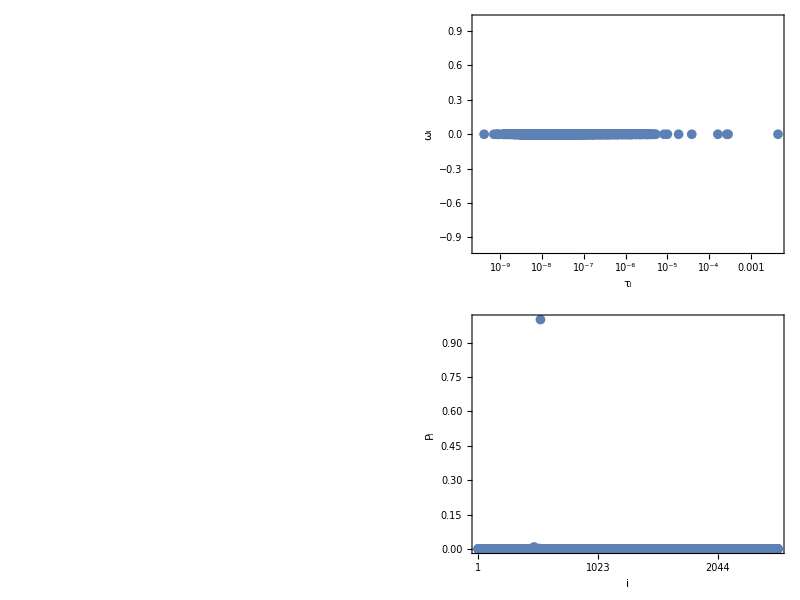

{100 (Ar_1)+O_1 H_1+10 (O_1 H_2),100 (Ar_1)+H_1+H_2+9 (O_1 H_2)+O_2,100 (Ar_1)+2 (H_2)+O_1 H_1+8 (O_1 H_2)+O_2,100 (Ar_1)+H_2+O_1+O_1 H_1+9 (O_1 H_2),100 (Ar_1)+H_1+O_1+10 (O_1 H_2)}

2334.49

6.37734

-4.10343×10^-10+0. ⅈ

0.708745

```mathematica
filebase="data/sweep2/40_40"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Total[spforms*#]&/@multiindices[[Reverse[Ordering[Abs[evecs[[-1]]]]][[1;;5]]]]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
Total[Abs[evals]^2]/Total[Total[A^2]]
```

7

4.05673×10^-7+0. ⅈ

4.48027×10^-14

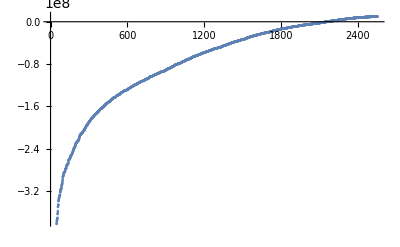

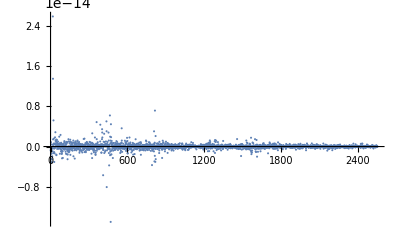

```mathematica
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
evals[[-1]]
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
ListPlot[Re[evals+1/(10^-7)]]
ListPlot[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]],PlotRange->All]
```

12

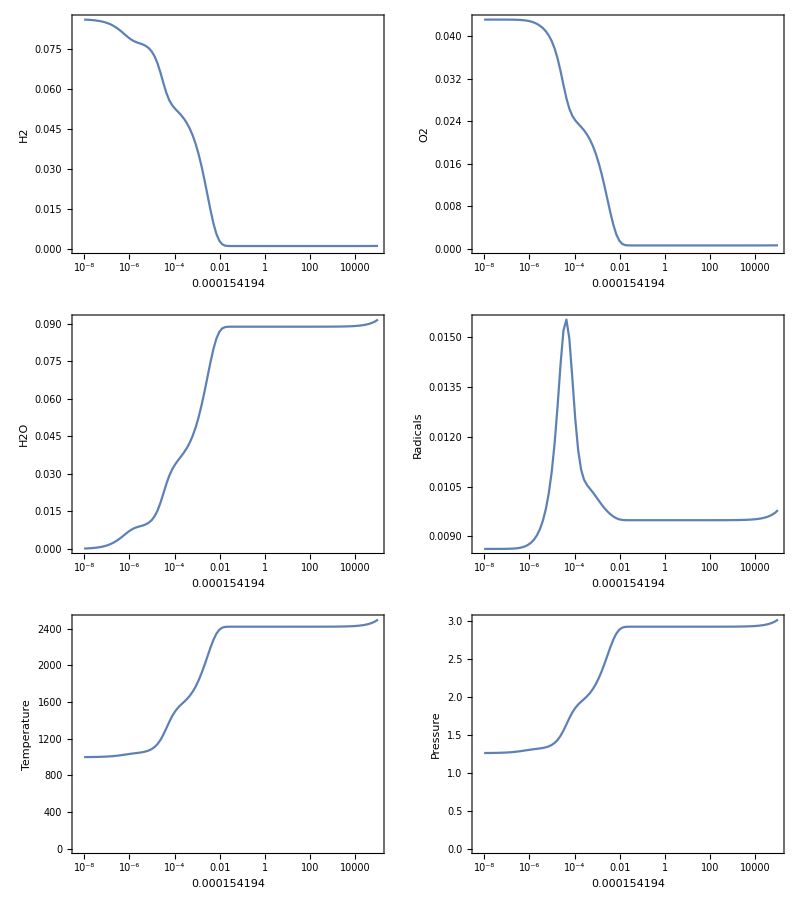

```mathematica
Nt=100;
t0=10.^-8;
t1=100000.;
filebase="data/sweep2/50_35";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
o2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[4]])/Total[#])&/@multiindices)];
h2norm=SparseArray[({#,#}&/@Range[dim])->(((#[[1]])/Total[#])&/@multiindices)];
h2onorm=SparseArray[({#,#}&/@Range[dim])->(((#[[6]])/Total[#])&/@multiindices)];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
temperaturenorm=SparseArray[({#,#}&/@Range[dim])->(temperatures)];
pressurenorm=SparseArray[({#,#}&/@Range[dim])->(pressures)];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]];((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]]),{t,times}];
h2=Transpose[{times,Total/@(states.h2norm)}];
o2=Transpose[{times,Total/@(states.o2norm)}];
h2o=Transpose[{times,Total/@(states.h2onorm)}];
radicals=Transpose[{times,Total/@(states.radicalnorm)}];
temp=Transpose[{times,Total/@(states.temperaturenorm)}];
pres=Transpose[{times,Total/@(states.pressurenorm)}];
Grid[{{ListLogLinearPlot[h2,Axes->False,Frame->True,FrameLabel->{t,"H2"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[o2,Axes->False,Frame->True,FrameLabel->{t,"O2"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True]},{ListLogLinearPlot[h2o,Axes->False,Frame->True,FrameLabel->{t,"H2O"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[radicals,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]},{ListLogLinearPlot[temp,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True],ListLogLinearPlot[pres,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True]}}]
```

```mathematica
v1=Diagonal[radicalnorm];
v2=Diagonal[radicalnorm].A;
Eigenvalues[{{v2.v1,v2.v2},{v1.v1,v1.v2}}]
```

{-1.31154×10^9,1.14665×10^9}

```mathematica
(
```

```mathematica
H=Outer[Times,Diagonal[radicalnorm],Diagonal[radicalnorm].A]+Transpose[Outer[Times,Diagonal[radicalnorm],Diagonal[radicalnorm].A]]
H2=Outer[Times,Diagonal[radicalnorm],Diagonal[radicalnorm].A]
N[Norm[Diagonal[radicalnorm].A]*Norm[Diagonal[radicalnorm]]]
Eigenvalues[H]
Eigenvalues[H2]
```

SparseArray[<8288641>, {2879, 2879}]

SparseArray[<8288641>, {2879, 2879}]

1.2291×10^9

{-1.31154×10^9,1.14665×10^9,-8.12478×10^-7,7.99503×10^-7,6.5561×10^-7,-6.10226×10^-7,-5.8233×10^-7,5.70262×10^-7,4.79586×10^-7,-4.7735×10^-7,-3.92525×10^-7,3.92417×10^-7,-2.94693×10^-7,2.81665×10^-7,1.94329×10^-7,-1.91326×10^-7,-1.65194×10^-7,1.53095×10^-7,-1.51113×10^-7,1.33026×10^-7,-1.26839×10^-7,1.19884×10^-7,1.1349×10^-7,-1.11785×10^-7,-9.18469×10^-8,8.4812×10^-8,-7.21222×10^-8,6.74472×10^-8,-6.04027×10^-8,5.71786×10^-8,5.10432×10^-8,-4.55586×10^-8,3.73167×10^-8,-3.66537×10^-8,2.68128×10^-8,-2.33329×10^-8,2.32046×10^-8,-2.20732×10^-8,2.1179×10^-8,-2.07702×10^-8,1.98591×10^-8,-1.88389×10^-8,1.79656×10^-8,-1.74853×10^-8,1.71607×10^-8,-1.70539×10^-8,1.62263×10^-8,-1.60202×10^-8,1.58546×10^-8,-1.57181×10^-8,-1.52416×10^-8,1.52403×10^-8,1.4521×10^-8,-1.45112×10^-8,1.39645×10^-8,-1.3801×10^-8,-1.34225×10^-8,-1.31847×10^-8,1.27056×10^-8,1.26601×10^-8,1.2609×10^-8,-1.25982×10^-8,1.23572×10^-8,-1.21291×10^-8,1.17895×10^-8,-1.16869×10^-8,-1.15574×10^-8,1.1428×10^-8,-1.12611×10^-8,-1.10937×10^-8,1.10479×10^-8,-1.09244×10^-8,1.08464×10^-8,-1.08407×10^-8,1.07057×10^-8,1.06578×10^-8,1.042×10^-8,-1.04085×10^-8,-1.03542×10^-8,1.01603×10^-8,1.00859×10^-8,-9.92404×10^-9,9.9183×10^-9,-9.73895×10^-9,9.68237×10^-9,-9.60595×10^-9,-9.54979×10^-9,9.54104×10^-9,9.37405×10^-9,-9.30038×10^-9,9.26235×10^-9,-9.16011×10^-9,8.97895×10^-9,8.92733×10^-9,-8.84609×10^-9,8.82927×10^-9,-8.74902×10^-9,-8.70222×10^-9,8.69828×10^-9,-8.53796×10^-9,-8.42824×10^-9,8.41037×10^-9,-8.27463×10^-9,8.24711×10^-9,-8.21346×10^-9,8.10335×10^-9,-8.02634×10^-9,8.01861×10^-9,7.99583×10^-9,-7.92733×10^-9,-7.83578×10^-9,7.81764×10^-9,-7.77496×10^-9,7.71426×10^-9,-7.66724×10^-9,7.59812×10^-9,-7.56577×10^-9,7.54781×10^-9,-7.51798×10^-9,7.45953×10^-9,-7.41627×10^-9,7.414×10^-9,7.32408×10^-9,-7.29138×10^-9,7.27833×10^-9,7.23786×10^-9,-7.23394×10^-9,-7.18885×10^-9,-7.08649×10^-9,7.06463×10^-9,7.01127×10^-9,-7.00502×10^-9,-6.96756×10^-9,-6.93799×10^-9,6.93125×10^-9,6.86976×10^-9,-6.8102×10^-9,-6.79879×10^-9,6.76091×10^-9,-6.71518×10^-9,6.70695×10^-9,6.68774×10^-9,-6.62833×10^-9,-6.60525×10^-9,6.5892×10^-9,6.52155×10^-9,-6.48901×10^-9,-6.42483×10^-9,6.37708×10^-9,-6.36383×10^-9,-6.32229×10^-9,6.32133×10^-9,6.30017×10^-9,-6.27416×10^-9,6.25403×10^-9,6.22107×10^-9,-6.15147×10^-9,6.14957×10^-9,6.11716×10^-9,-6.0474×10^-9,6.02564×10^-9,-6.01648×10^-9,-5.99733×10^-9,5.98691×10^-9,-5.94438×10^-9,5.94333×10^-9,-5.93973×10^-9,5.88003×10^-9,5.85794×10^-9,-5.84927×10^-9,5.81212×10^-9,-5.78937×10^-9,-5.7777×10^-9,5.76967×10^-9,5.73383×10^-9,-5.70626×10^-9,5.70563×10^-9,-5.64331×10^-9,5.62488×10^-9,5.6028×10^-9,-5.57591×10^-9,5.571×10^-9,-5.54945×10^-9,-5.53152×10^-9,-5.51953×10^-9,5.51171×10^-9,5.48107×10^-9,-5.45682×10^-9,5.44248×10^-9,5.42142×10^-9,-5.40036×10^-9,5.36006×10^-9,-5.35468×10^-9,-5.31734×10^-9,5.29432×10^-9,-5.28218×10^-9,5.27138×10^-9,5.24672×10^-9,-5.24507×10^-9,5.23795×10^-9,-5.22892×10^-9,5.21278×10^-9,-5.20545×10^-9,5.17477×10^-9,-5.16102×10^-9,-5.14517×10^-9,-5.11664×10^-9,5.09479×10^-9,-5.0842×10^-9,-5.05377×10^-9,5.04274×10^-9,5.03648×10^-9,-5.0345×10^-9,4.9859×10^-9,-4.97482×10^-9,4.96253×10^-9,-4.96122×10^-9,4.92511×10^-9,-4.92126×10^-9,-4.90817×10^-9,-4.89214×10^-9,4.89058×10^-9,-4.87181×10^-9,-4.85369×10^-9,4.84902×10^-9,4.82573×10^-9,4.82256×10^-9,-4.8012×10^-9,4.78235×10^-9,4.78046×10^-9,-4.77277×10^-9,4.75773×10^-9,-4.75685×10^-9,-4.72676×10^-9,4.69739×10^-9,4.69597×10^-9,-4.6958×10^-9,4.65963×10^-9,-4.65169×10^-9,4.63335×10^-9,-4.60053×10^-9,4.59296×10^-9,-4.58651×10^-9,-4.58236×10^-9,4.57809×10^-9,4.56894×10^-9,-4.54093×10^-9,4.53074×10^-9,-4.52453×10^-9,4.49915×10^-9,-4.494×10^-9,4.47125×10^-9,-4.46537×10^-9,4.45534×10^-9,-4.43566×10^-9,-4.42202×10^-9,4.42125×10^-9,4.41235×10^-9,-4.3954×10^-9,4.37767×10^-9,-4.37586×10^-9,-4.36402×10^-9,4.3614×10^-9,-4.34703×10^-9,4.33267×10^-9,-4.31953×10^-9,4.31571×10^-9,-4.29309×10^-9,4.28947×10^-9,-4.27454×10^-9,4.27013×10^-9,-4.26218×10^-9,-4.24336×10^-9,4.23771×10^-9,4.23093×10^-9,-4.22426×10^-9,4.20411×10^-9,-4.19698×10^-9,-4.18172×10^-9,4.17607×10^-9,-4.16275×10^-9,4.14979×10^-9,-4.13923×10^-9,4.12027×10^-9,-4.10579×10^-9,4.09672×10^-9,-4.09062×10^-9,4.08876×10^-9,-4.07888×10^-9,4.07313×10^-9,-4.07005×10^-9,4.05243×10^-9,-4.03898×10^-9,4.03362×10^-9,4.02706×10^-9,-4.02054×10^-9,-4.01489×10^-9,3.99906×10^-9,-3.9855×10^-9,-3.9713×10^-9,3.96107×10^-9,3.95688×10^-9,-3.94727×10^-9,3.93812×10^-9,3.92888×10^-9,-3.92509×10^-9,-3.92188×10^-9,3.90555×10^-9,-3.90332×10^-9,3.89272×10^-9,-3.8906×10^-9,3.88066×10^-9,3.86404×10^-9,-3.85875×10^-9,-3.84773×10^-9,3.84617×10^-9,3.83022×10^-9,3.82365×10^-9,-3.82253×10^-9,3.81114×10^-9,-3.8005×10^-9,-3.79359×10^-9,3.79118×10^-9,3.76702×10^-9,-3.75958×10^-9,-3.74899×10^-9,3.74606×10^-9,-3.72219×10^-9,3.71958×10^-9,3.7149×10^-9,-3.71214×10^-9,-3.70706×10^-9,3.69257×10^-9,-3.68348×10^-9,-3.67633×10^-9,3.67456×10^-9,3.65649×10^-9,-3.64989×10^-9,3.63866×10^-9,-3.63279×10^-9,-3.62632×10^-9,3.62233×10^-9,3.61696×10^-9,-3.61017×10^-9,-3.5997×10^-9,3.59242×10^-9,-3.59063×10^-9,3.58592×10^-9,3.56965×10^-9,-3.55549×10^-9,-3.54583×10^-9,3.54482×10^-9,3.53472×10^-9,-3.52502×10^-9,3.52241×10^-9,-3.50711×10^-9,3.49991×10^-9,-3.49288×10^-9,3.48528×10^-9,-3.48265×10^-9,3.47491×10^-9,-3.47434×10^-9,3.45955×10^-9,-3.45718×10^-9,3.45304×10^-9,-3.44772×10^-9,-3.43897×10^-9,3.43089×10^-9,3.42753×10^-9,-3.41821×10^-9,3.41784×10^-9,-3.40553×10^-9,3.39909×10^-9,-3.38676×10^-9,3.38514×10^-9,-3.38201×10^-9,3.37634×10^-9,-3.3748×10^-9,3.37008×10^-9,3.35781×10^-9,-3.341×10^-9,-3.33548×10^-9,3.33294×10^-9,3.32774×10^-9,-3.32374×10^-9,3.31338×10^-9,-3.31302×10^-9,-3.30075×10^-9,3.29474×10^-9,-3.29389×10^-9,3.29116×10^-9,-3.28673×10^-9,-3.27312×10^-9,-3.26529×10^-9,3.26304×10^-9,-3.24698×10^-9,3.24597×10^-9,3.24545×10^-9,-3.23696×10^-9,3.22606×10^-9,-3.21482×10^-9,-3.21246×10^-9,3.20925×10^-9,-3.20053×10^-9,3.20046×10^-9,3.18908×10^-9,-3.18061×10^-9,3.17902×10^-9,-3.17283×10^-9,3.16986×10^-9,-3.15124×10^-9,-3.14444×10^-9,3.14369×10^-9,-3.14003×10^-9,3.13889×10^-9,-3.12915×10^-9,3.12441×10^-9,3.12129×10^-9,-3.10898×10^-9,3.10556×10^-9,-3.09353×10^-9,3.08648×10^-9,-3.08602×10^-9,3.08369×10^-9,-3.07382×10^-9,-3.06803×10^-9,3.06535×10^-9,-3.0581×10^-9,3.0572×10^-9,-3.04792×10^-9,3.03546×10^-9,-3.0347×10^-9,-3.03045×10^-9,3.0272×10^-9,-3.02067×10^-9,3.01426×10^-9,3.0081×10^-9,-3.00793×10^-9,3.00235×10^-9,-2.99805×10^-9,2.99195×10^-9,-2.98785×10^-9,-2.98222×10^-9,2.97938×10^-9,2.97586×10^-9,2.97257×10^-9,-2.96758×10^-9,-2.9628×10^-9,2.95895×10^-9,-2.95107×10^-9,2.94916×10^-9,2.93897×10^-9,2.92414×10^-9,-2.92221×10^-9,-2.91877×10^-9,2.91622×10^-9,2.91573×10^-9,-2.9104×10^-9,-2.90651×10^-9,2.90041×10^-9,-2.89945×10^-9,2.88844×10^-9,-2.88134×10^-9,2.88014×10^-9,2.86849×10^-9,-2.86179×10^-9,-2.85797×10^-9,2.85674×10^-9,-2.84965×10^-9,2.84365×10^-9,2.84069×10^-9,-2.83915×10^-9,-2.83238×10^-9,2.82686×10^-9,2.81424×10^-9,-2.81294×10^-9,2.80943×10^-9,-2.8042×10^-9,-2.7981×10^-9,-2.79343×10^-9,-2.78864×10^-9,2.78511×10^-9,2.7783×10^-9,-2.77569×10^-9,2.77132×10^-9,-2.76119×10^-9,2.75968×10^-9,-2.75784×10^-9,2.75316×10^-9,-2.74928×10^-9,2.74828×10^-9,-2.73859×10^-9,-2.73343×10^-9,2.73096×10^-9,2.72053×10^-9,2.71739×10^-9,-2.71394×10^-9,2.71227×10^-9,-2.71117×10^-9,2.70469×10^-9,-2.70219×10^-9,2.69827×10^-9,-2.6924×10^-9,-2.68528×10^-9,2.68132×10^-9,-2.67476×10^-9,2.67421×10^-9,-2.66858×10^-9,2.66199×10^-9,-2.66129×10^-9,2.65731×10^-9,-2.65557×10^-9,2.65063×10^-9,-2.64431×10^-9,2.63466×10^-9,2.63269×10^-9,2.62764×10^-9,-2.62542×10^-9,2.62289×10^-9,-2.61972×10^-9,2.61025×10^-9,-2.6095×10^-9,-2.60162×10^-9,2.59345×10^-9,-2.59203×10^-9,2.58697×10^-9,-2.58356×10^-9,2.57693×10^-9,-2.57596×10^-9,2.56893×10^-9,-2.56474×10^-9,2.56123×10^-9,2.55549×10^-9,-2.55278×10^-9,-2.54967×10^-9,2.54961×10^-9,-2.5425×10^-9,-2.53738×10^-9,2.53701×10^-9,-2.53221×10^-9,2.52698×10^-9,2.52465×10^-9,-2.52183×10^-9,2.52022×10^-9,2.5075×10^-9,-2.50368×10^-9,2.49958×10^-9,-2.49701×10^-9,-2.49054×10^-9,2.4835×10^-9,-2.47885×10^-9,2.478×10^-9,2.47332×10^-9,2.46595×10^-9,2.46492×10^-9,-2.46046×10^-9,2.45662×10^-9,-2.45223×10^-9,-2.44845×10^-9,-2.44101×10^-9,2.43878×10^-9,-2.43853×10^-9,2.43192×10^-9,-2.4304×10^-9,2.42699×10^-9,-2.42055×10^-9,2.41649×10^-9,-2.41556×10^-9,2.41307×10^-9,2.40584×10^-9,-2.40521×10^-9,-2.38964×10^-9,2.38764×10^-9,-2.38659×10^-9,2.38484×10^-9,-2.38309×10^-9,-2.37681×10^-9,2.37187×10^-9,2.36654×10^-9,2.36445×10^-9,-2.3615×10^-9,2.36139×10^-9,-2.36038×10^-9,2.35875×10^-9,-2.35333×10^-9,2.3516×10^-9,-2.35068×10^-9,-2.34173×10^-9,2.33553×10^-9,2.33424×10^-9,-2.33195×10^-9,2.32877×10^-9,-2.32077×10^-9,2.31836×10^-9,-2.31567×10^-9,2.30979×10^-9,2.30619×10^-9,-2.30552×10^-9,2.29871×10^-9,2.29479×10^-9,-2.29232×10^-9,-2.28965×10^-9,2.28632×10^-9,2.28328×10^-9,-2.28081×10^-9,-2.27741×10^-9,-2.27173×10^-9,2.27081×10^-9,2.26134×10^-9,-2.25998×10^-9,-2.25718×10^-9,-2.2541×10^-9,2.2531×10^-9,2.24807×10^-9,-2.24341×10^-9,-2.23838×10^-9,2.23532×10^-9,2.23335×10^-9,2.23211×10^-9,-2.22669×10^-9,-2.22348×10^-9,2.22002×10^-9,2.21674×10^-9,-2.21558×10^-9,2.20859×10^-9,-2.20686×10^-9,-2.19996×10^-9,2.19701×10^-9,2.19373×10^-9,2.19187×10^-9,-2.18568×10^-9,-2.1823×10^-9,2.17973×10^-9,-2.1788×10^-9,2.17789×10^-9,-2.17618×10^-9,-2.1719×10^-9,2.16966×10^-9,2.16293×10^-9,-2.16271×10^-9,2.15548×10^-9,-2.15334×10^-9,2.15085×10^-9,-2.14643×10^-9,2.14497×10^-9,-2.14224×10^-9,2.1355×10^-9,-2.13049×10^-9,-2.12972×10^-9,2.12576×10^-9,-2.12406×10^-9,2.12204×10^-9,-2.12006×10^-9,2.11063×10^-9,2.10643×10^-9,-2.1059×10^-9,-2.10153×10^-9,-2.09938×10^-9,-2.09726×10^-9,2.09553×10^-9,2.09347×10^-9,2.08981×10^-9,2.08698×10^-9,-2.08635×10^-9,-2.08173×10^-9,2.07585×10^-9,-2.07374×10^-9,2.0729×10^-9,-2.06876×10^-9,2.06723×10^-9,-2.06381×10^-9,2.06035×10^-9,-2.05934×10^-9,2.05503×10^-9,-2.0513×10^-9,-2.04464×10^-9,2.04423×10^-9,2.03755×10^-9,-2.03691×10^-9,-2.0344×10^-9,2.03408×10^-9,-2.02905×10^-9,2.02632×10^-9,2.02231×10^-9,-2.01609×10^-9,2.01483×10^-9,2.0131×10^-9,-2.00953×10^-9,-2.00532×10^-9,-2.00334×10^-9,2.00216×10^-9,1.99863×10^-9,-1.9944×10^-9,1.99294×10^-9,-1.98691×10^-9,1.98317×10^-9,-1.98313×10^-9,1.98179×10^-9,-1.98135×10^-9,1.98119×10^-9,1.97744×10^-9,-1.97729×10^-9,-1.96725×10^-9,1.96701×10^-9,1.96298×10^-9,-1.96178×10^-9,1.9574×10^-9,-1.95666×10^-9,1.9505×10^-9,-1.94996×10^-9,-1.94866×10^-9,1.94701×10^-9,1.93983×10^-9,-1.93815×10^-9,-1.93249×10^-9,1.92841×10^-9,1.92608×10^-9,-1.92546×10^-9,1.92479×10^-9,-1.92302×10^-9,1.91896×10^-9,1.91302×10^-9,-1.91173×10^-9,1.90809×10^-9,-1.90766×10^-9,-1.90579×10^-9,-1.89938×10^-9,1.89919×10^-9,1.89685×10^-9,-1.89638×10^-9,-1.89083×10^-9,1.88807×10^-9,1.88426×10^-9,-1.87896×10^-9,-1.87686×10^-9,1.87681×10^-9,1.87593×10^-9,-1.86906×10^-9,1.86667×10^-9,-1.86451×10^-9,-1.86201×10^-9,1.85981×10^-9,-1.8547×10^-9,1.8517×10^-9,1.85065×10^-9,-1.84941×10^-9,-1.84716×10^-9,1.84307×10^-9,-1.83857×10^-9,1.83333×10^-9,-1.82901×10^-9,-1.82833×10^-9,1.82771×10^-9,-1.82463×10^-9,1.82248×10^-9,-1.8196×10^-9,1.81887×10^-9,-1.81658×10^-9,1.81528×10^-9,1.81114×10^-9,-1.8103×10^-9,1.80724×10^-9,-1.80146×10^-9,1.79673×10^-9,-1.79585×10^-9,1.79504×10^-9,1.79032×10^-9,-1.78846×10^-9,1.78552×10^-9,1.78358×10^-9,-1.78349×10^-9,-1.78056×10^-9,1.77818×10^-9,-1.77582×10^-9,1.77424×10^-9,-1.7702×10^-9,1.76916×10^-9,-1.76481×10^-9,1.76449×10^-9,-1.76348×10^-9,-1.76104×10^-9,1.75626×10^-9,1.75342×10^-9,-1.7459×10^-9,1.74211×10^-9,-1.74067×10^-9,1.73981×10^-9,1.73918×10^-9,-1.73676×10^-9,1.7365×10^-9,-1.73323×10^-9,1.72767×10^-9,-1.72573×10^-9,1.72565×10^-9,-1.72412×10^-9,1.71747×10^-9,-1.71729×10^-9,1.7115×10^-9,-1.71064×10^-9,1.70603×10^-9,-1.70545×10^-9,1.70455×10^-9,1.70095×10^-9,-1.70074×10^-9,-1.69941×10^-9,-1.6964×10^-9,1.69331×10^-9,-1.68769×10^-9,1.68672×10^-9,-1.68569×10^-9,-1.68278×10^-9,1.68268×10^-9,-1.67712×10^-9,1.67327×10^-9,-1.67279×10^-9,1.67205×10^-9,-1.66842×10^-9,1.66392×10^-9,1.66138×10^-9,-1.65868×10^-9,1.65644×10^-9,-1.65567×10^-9,1.64908×10^-9,-1.64858×10^-9,-1.64749×10^-9,1.64707×10^-9,-1.64502×10^-9,-1.64241×10^-9,1.63996×10^-9,1.63794×10^-9,1.63444×10^-9,-1.63386×10^-9,-1.63095×10^-9,1.62587×10^-9,-1.62585×10^-9,1.6249×10^-9,-1.62329×10^-9,1.62225×10^-9,-1.61976×10^-9,-1.61613×10^-9,-1.61123×10^-9,1.61106×10^-9,-1.60872×10^-9,1.60775×10^-9,1.60395×10^-9,1.6018×10^-9,-1.60005×10^-9,1.5981×10^-9,-1.59528×10^-9,-1.5896×10^-9,1.58947×10^-9,1.58797×10^-9,-1.58616×10^-9,-1.58123×10^-9,1.58062×10^-9,-1.57803×10^-9,1.57702×10^-9,-1.57296×10^-9,1.57189×10^-9,-1.56777×10^-9,1.5672×10^-9,-1.56634×10^-9,-1.56077×10^-9,1.56069×10^-9,1.55652×10^-9,1.55602×10^-9,-1.55285×10^-9,1.55072×10^-9,-1.54978×10^-9,1.54688×10^-9,-1.54585×10^-9,1.54468×10^-9,-1.54419×10^-9,1.54211×10^-9,-1.54114×10^-9,1.54112×10^-9,-1.53489×10^-9,1.53291×10^-9,-1.53092×10^-9,1.53029×10^-9,1.52558×10^-9,-1.524×10^-9,1.51978×10^-9,-1.51842×10^-9,1.51656×10^-9,-1.51477×10^-9,-1.51405×10^-9,1.51213×10^-9,1.51082×10^-9,-1.51081×10^-9,-1.50047×10^-9,1.50046×10^-9,1.49912×10^-9,-1.4984×10^-9,1.49578×10^-9,-1.49404×10^-9,1.49067×10^-9,1.49023×10^-9,-1.48755×10^-9,-1.48406×10^-9,-1.48128×10^-9,1.48028×10^-9,-1.47852×10^-9,1.47458×10^-9,-1.47046×10^-9,1.47019×10^-9,-1.46924×10^-9,-1.46707×10^-9,1.46611×10^-9,-1.46475×10^-9,-1.46279×10^-9,1.46211×10^-9,1.46082×10^-9,-1.45838×10^-9,1.45524×10^-9,-1.45514×10^-9,1.45219×10^-9,-1.44775×10^-9,1.44615×10^-9,1.44325×10^-9,-1.44312×10^-9,-1.4395×10^-9,1.43765×10^-9,1.43732×10^-9,-1.4368×10^-9,-1.43505×10^-9,-1.43248×10^-9,-1.42786×10^-9,-1.4273×10^-9,1.42639×10^-9,1.42516×10^-9,1.42467×10^-9,1.42263×10^-9,-1.42005×10^-9,-1.41592×10^-9,1.41571×10^-9,1.41202×10^-9,1.40982×10^-9,-1.40874×10^-9,-1.40831×10^-9,1.40641×10^-9,1.40627×10^-9,-1.40525×10^-9,-1.40401×10^-9,1.39984×10^-9,1.39635×10^-9,-1.39547×10^-9,-1.39524×10^-9,1.394×10^-9,1.3912×10^-9,-1.38912×10^-9,1.38702×10^-9,-1.38455×10^-9,-1.38194×10^-9,1.37669×10^-9,-1.37571×10^-9,-1.37453×10^-9,-1.37303×10^-9,1.37274×10^-9,1.37003×10^-9,1.36918×10^-9,-1.36331×10^-9,1.36319×10^-9,1.36144×10^-9,-1.3611×10^-9,1.35878×10^-9,-1.35579×10^-9,1.3533×10^-9,-1.35166×10^-9,1.35029×10^-9,1.34789×10^-9,-1.34629×10^-9,1.34301×10^-9,-1.34115×10^-9,-1.33748×10^-9,-1.33485×10^-9,1.33471×10^-9,1.33244×10^-9,-1.33219×10^-9,-1.33019×10^-9,1.32702×10^-9,1.32589×10^-9,-1.32589×10^-9,1.32426×10^-9,1.3226×10^-9,-1.31948×10^-9,1.3192×10^-9,1.31392×10^-9,-1.31179×10^-9,-1.30906×10^-9,1.30758×10^-9,-1.30579×10^-9,1.30483×10^-9,-1.30399×10^-9,1.3028×10^-9,-1.30266×10^-9,-1.3017×10^-9,1.29873×10^-9,-1.29517×10^-9,-1.29318×10^-9,1.29289×10^-9,-1.29015×10^-9,1.28742×10^-9,1.28403×10^-9,-1.28317×10^-9,-1.28126×10^-9,1.2797×10^-9,-1.27851×10^-9,1.27813×10^-9,-1.27767×10^-9,1.27746×10^-9,-1.27526×10^-9,1.271×10^-9,1.26902×10^-9,-1.26899×10^-9,1.26681×10^-9,-1.26589×10^-9,1.2619×10^-9,-1.26021×10^-9,-1.25722×10^-9,1.25513×10^-9,1.25228×10^-9,-1.25132×10^-9,-1.24943×10^-9,1.24929×10^-9,1.24876×10^-9,-1.24468×10^-9,1.24367×10^-9,1.24246×10^-9,-1.24159×10^-9,1.23797×10^-9,-1.23688×10^-9,1.2361×10^-9,-1.23478×10^-9,1.23296×10^-9,-1.2326×10^-9,-1.2301×10^-9,1.22942×10^-9,-1.22877×10^-9,-1.22244×10^-9,1.222×10^-9,-1.22021×10^-9,1.21826×10^-9,1.21623×10^-9,-1.21363×10^-9,1.2135×10^-9,-1.21187×10^-9,1.20917×10^-9,-1.20771×10^-9,1.20563×10^-9,-1.20448×10^-9,-1.20187×10^-9,1.20133×10^-9,-1.20092×10^-9,1.19991×10^-9,-1.19833×10^-9,1.19806×10^-9,-1.19549×10^-9,-1.19201×10^-9,1.19125×10^-9,1.18925×10^-9,-1.1888×10^-9,1.18814×10^-9,-1.18716×10^-9,1.18405×10^-9,-1.1823×10^-9,1.18004×10^-9,-1.17958×10^-9,-1.17845×10^-9,1.17727×10^-9,1.17455×10^-9,-1.1735×10^-9,-1.17085×10^-9,-1.16988×10^-9,1.16984×10^-9,1.1688×10^-9,1.16775×10^-9,-1.16476×10^-9,-1.16323×10^-9,1.16219×10^-9,1.16039×10^-9,-1.15776×10^-9,1.15739×10^-9,-1.15615×10^-9,1.15346×10^-9,-1.15145×10^-9,-1.14853×10^-9,1.1484×10^-9,1.14528×10^-9,-1.14374×10^-9,-1.14132×10^-9,1.14111×10^-9,-1.14016×10^-9,1.13727×10^-9,-1.13708×10^-9,1.13624×10^-9,-1.13514×10^-9,1.13484×10^-9,1.13034×10^-9,-1.12852×10^-9,1.12818×10^-9,-1.12795×10^-9,-1.12531×10^-9,1.1249×10^-9,1.12275×10^-9,-1.11906×10^-9,1.1184×10^-9,-1.11506×10^-9,1.115×10^-9,-1.11299×10^-9,-1.11183×10^-9,1.11156×10^-9,-1.10979×10^-9,1.10889×10^-9,1.10746×10^-9,-1.10339×10^-9,1.1033×10^-9,-1.10089×10^-9,-1.09925×10^-9,1.09783×10^-9,-1.09751×10^-9,1.09558×10^-9,-1.09486×10^-9,1.09378×10^-9,1.09287×10^-9,-1.08787×10^-9,-1.08752×10^-9,1.087×10^-9,-1.08296×10^-9,1.08274×10^-9,1.08035×10^-9,-1.07992×10^-9,1.0761×10^-9,-1.07594×10^-9,1.07436×10^-9,-1.07429×10^-9,1.07262×10^-9,-1.07182×10^-9,1.06993×10^-9,1.06819×10^-9,-1.06785×10^-9,-1.06613×10^-9,1.06457×10^-9,-1.06332×10^-9,-1.0623×10^-9,1.06022×10^-9,-1.0586×10^-9,1.05817×10^-9,1.05539×10^-9,-1.05193×10^-9,1.05189×10^-9,1.05075×10^-9,-1.04938×10^-9,1.04847×10^-9,-1.04479×10^-9,1.04418×10^-9,1.04318×10^-9,-1.04035×10^-9,1.03876×10^-9,-1.03793×10^-9,-1.03702×10^-9,1.03532×10^-9,-1.03422×10^-9,1.03224×10^-9,-1.03187×10^-9,-1.03063×10^-9,1.02974×10^-9,-1.02911×10^-9,1.02855×10^-9,-1.02523×10^-9,1.02406×10^-9,1.02305×10^-9,-1.02028×10^-9,1.02×10^-9,-1.01928×10^-9,-1.01745×10^-9,1.01732×10^-9,1.01437×10^-9,-1.01391×10^-9,1.01274×10^-9,1.01065×10^-9,-1.01017×10^-9,-1.00862×10^-9,-1.0062×10^-9,1.0062×10^-9,1.00492×10^-9,-1.00326×10^-9,1.00141×10^-9,-1.00041×10^-9,9.99176×10^-10,9.97592×10^-10,-9.96203×10^-10,9.9514×10^-10,-9.93392×10^-10,9.92476×10^-10,-9.91582×10^-10,-9.88886×10^-10,9.87457×10^-10,9.86247×10^-10,-9.84034×10^-10,-9.82423×10^-10,-9.81638×10^-10,9.80992×10^-10,9.79891×10^-10,-9.78389×10^-10,9.75574×10^-10,-9.74382×10^-10,-9.74086×10^-10,9.72402×10^-10,9.7091×10^-10,-9.70284×10^-10,9.68766×10^-10,-9.68146×10^-10,-9.67185×10^-10,9.65411×10^-10,-9.62073×10^-10,9.61705×10^-10,-9.59462×10^-10,-9.58207×10^-10,9.57538×10^-10,-9.54278×10^-10,9.54077×10^-10,-9.53298×10^-10,9.51819×10^-10,9.51304×10^-10,-9.50589×10^-10,9.50054×10^-10,-9.47475×10^-10,9.46609×10^-10,-9.46282×10^-10,9.44172×10^-10,-9.42624×10^-10,-9.39538×10^-10,9.38229×10^-10,9.37707×10^-10,9.36381×10^-10,-9.35086×10^-10,9.34259×10^-10,9.33866×10^-10,-9.33098×10^-10,-9.30872×10^-10,9.28008×10^-10,-9.26657×10^-10,9.26108×10^-10,-9.23651×10^-10,9.23553×10^-10,-9.21687×10^-10,-9.21006×10^-10,9.20689×10^-10,9.20118×10^-10,9.17482×10^-10,-9.15745×10^-10,-9.15345×10^-10,-9.12167×10^-10,-9.11459×10^-10,9.1127×10^-10,-9.10959×10^-10,9.09457×10^-10,9.0616×10^-10,-9.04539×10^-10,-9.02549×10^-10,-9.01648×10^-10,9.01083×10^-10,8.99354×10^-10,8.98401×10^-10,-8.96923×10^-10,8.94648×10^-10,-8.9452×10^-10,8.91924×10^-10,-8.9172×10^-10,-8.90648×10^-10,8.90004×10^-10,-8.88765×10^-10,8.87277×10^-10,-8.86701×10^-10,8.85447×10^-10,-8.84242×10^-10,8.82112×10^-10,8.81059×10^-10,-8.80712×10^-10,-8.79929×10^-10,8.79397×10^-10,8.75401×10^-10,-8.73296×10^-10,8.7288×10^-10,-8.72784×10^-10,8.71509×10^-10,-8.70631×10^-10,-8.69735×10^-10,8.68778×10^-10,8.67642×10^-10,-8.66722×10^-10,8.65423×10^-10,8.63944×10^-10,-8.63065×10^-10,-8.60237×10^-10,8.60231×10^-10,-8.59396×10^-10,8.56951×10^-10,8.5445×10^-10,-8.54215×10^-10,8.52123×10^-10,-8.51385×10^-10,8.49981×10^-10,-8.48745×10^-10,-8.47557×10^-10,-8.45458×10^-10,8.43913×10^-10,8.43008×10^-10,-8.42165×10^-10,8.42064×10^-10,8.40126×10^-10,-8.39601×10^-10,8.39142×10^-10,-8.38753×10^-10,8.37391×10^-10,-8.36644×10^-10,-8.34588×10^-10,8.34124×10^-10,8.33065×10^-10,-8.32245×10^-10,-8.29189×10^-10,8.28821×10^-10,8.2651×10^-10,8.25518×10^-10,-8.24532×10^-10,8.24037×10^-10,-8.23555×10^-10,8.21955×10^-10,-8.21594×10^-10,-8.20644×10^-10,8.18342×10^-10,-8.18231×10^-10,-8.16257×10^-10,8.15877×10^-10,8.14145×10^-10,8.13684×10^-10,-8.12781×10^-10,-8.1038×10^-10,8.10013×10^-10,8.09374×10^-10,8.08292×10^-10,-8.07957×10^-10,-8.06592×10^-10,-8.06075×10^-10,8.03382×10^-10,8.01996×10^-10,-8.01023×10^-10,7.99637×10^-10,-7.98439×10^-10,7.98035×10^-10,-7.97119×10^-10,7.95901×10^-10,-7.95505×10^-10,7.94305×10^-10,-7.93451×10^-10,7.91413×10^-10,-7.90849×10^-10,-7.89877×10^-10,7.88597×10^-10,7.86152×10^-10,-7.86051×10^-10,-7.84589×10^-10,7.83526×10^-10,-7.82373×10^-10,7.80315×10^-10,-7.79664×10^-10,7.77556×10^-10,7.77027×10^-10,-7.75921×10^-10,-7.75095×10^-10,7.75083×10^-10,-7.74348×10^-10,7.72988×10^-10,7.72284×10^-10,-7.71829×10^-10,-7.70054×10^-10,7.69231×10^-10,-7.67347×10^-10,-7.66086×10^-10,7.65545×10^-10,-7.63396×10^-10,7.62456×10^-10,-7.61092×10^-10,-7.58288×10^-10,7.57922×10^-10,7.57005×10^-10,7.56764×10^-10,-7.55845×10^-10,-7.55131×10^-10,7.54803×10^-10,7.52542×10^-10,-7.51873×10^-10,7.51377×10^-10,-7.50677×10^-10,7.48898×10^-10,-7.47922×10^-10,-7.46757×10^-10,7.46329×10^-10,7.4465×10^-10,7.43173×10^-10,-7.43135×10^-10,7.41131×10^-10,-7.40972×10^-10,-7.39752×10^-10,7.38481×10^-10,-7.38463×10^-10,7.37179×10^-10,-7.36334×10^-10,7.36034×10^-10,7.32987×10^-10,-7.31968×10^-10,7.31422×10^-10,-7.30186×10^-10,7.28909×10^-10,-7.28583×10^-10,-7.26544×10^-10,7.26455×10^-10,7.25188×10^-10,-7.24864×10^-10,7.23516×10^-10,-7.21041×10^-10,7.20621×10^-10,-7.19986×10^-10,-7.18998×10^-10,7.18853×10^-10,-7.16357×10^-10,7.16197×10^-10,7.14176×10^-10,-7.13888×10^-10,7.12481×10^-10,-7.11619×10^-10,-7.10317×10^-10,-7.10004×10^-10,7.09988×10^-10,7.09788×10^-10,-7.06812×10^-10,7.06732×10^-10,7.05736×10^-10,7.04304×10^-10,-7.04041×10^-10,-7.02254×10^-10,7.01634×10^-10,-7.01325×10^-10,7.00101×10^-10,6.99112×10^-10,-6.98791×10^-10,-6.97991×10^-10,-6.96179×10^-10,6.95666×10^-10,-6.94332×10^-10,6.92942×10^-10,-6.92772×10^-10,6.90843×10^-10,-6.90093×10^-10,6.89014×10^-10,6.88738×10^-10,-6.86898×10^-10,-6.85547×10^-10,6.83856×10^-10,-6.82958×10^-10,6.81363×10^-10,6.81253×10^-10,-6.80238×10^-10,6.7914×10^-10,-6.79006×10^-10,-6.76678×10^-10,6.76496×10^-10,6.75686×10^-10,-6.75674×10^-10,-6.72559×10^-10,6.71633×10^-10,-6.71191×10^-10,6.70094×10^-10,-6.69938×10^-10,6.69552×10^-10,-6.68726×10^-10,6.68307×10^-10,6.6669×10^-10,-6.6558×10^-10,6.6473×10^-10,-6.62938×10^-10,6.62159×10^-10,-6.61705×10^-10,6.61132×10^-10,-6.60472×10^-10,6.58894×10^-10,-6.57849×10^-10,-6.56914×10^-10,-6.5558×10^-10,6.55477×10^-10,-6.53679×10^-10,6.52954×10^-10,-6.5275×10^-10,6.52554×10^-10,6.50532×10^-10,6.49977×10^-10,-6.48079×10^-10,6.46954×10^-10,-6.46736×10^-10,-6.46395×10^-10,6.45137×10^-10,-6.45064×10^-10,-6.43612×10^-10,6.42991×10^-10,-6.42687×10^-10,-6.41754×10^-10,6.41493×10^-10,6.39913×10^-10,-6.39188×10^-10,6.38976×10^-10,6.37686×10^-10,-6.37007×10^-10,-6.35812×10^-10,6.35267×10^-10,6.34455×10^-10,-6.3387×10^-10,6.31493×10^-10,-6.3074×10^-10,6.3044×10^-10,6.2854×10^-10,-6.28059×10^-10,-6.27768×10^-10,6.26774×10^-10,-6.26075×10^-10,6.23186×10^-10,-6.23095×10^-10,6.2142×10^-10,-6.20601×10^-10,6.2055×10^-10,6.19741×10^-10,-6.19433×10^-10,-6.18791×10^-10,6.17806×10^-10,-6.1734×10^-10,-6.14914×10^-10,6.14778×10^-10,6.13495×10^-10,-6.1278×10^-10,6.11867×10^-10,-6.10951×10^-10,-6.09552×10^-10,6.09124×10^-10,6.0877×10^-10,-6.07726×10^-10,6.06818×10^-10,-6.06786×10^-10,-6.04738×10^-10,6.03759×10^-10,6.02524×10^-10,6.01915×10^-10,-6.01792×10^-10,-6.01109×10^-10,-5.99047×10^-10,5.9853×10^-10,-5.97653×10^-10,5.97642×10^-10,5.96733×10^-10,-5.95834×10^-10,5.94323×10^-10,-5.93326×10^-10,-5.92646×10^-10,5.92586×10^-10,-5.9163×10^-10,5.90874×10^-10,5.89044×10^-10,-5.88289×10^-10,5.87929×10^-10,-5.86925×10^-10,5.86399×10^-10,-5.86025×10^-10,5.83547×10^-10,-5.83098×10^-10,-5.82051×10^-10,5.81771×10^-10,5.79909×10^-10,5.78193×10^-10,-5.77545×10^-10,5.76901×10^-10,-5.76646×10^-10,-5.74226×10^-10,5.74068×10^-10,-5.7313×10^-10,5.7288×10^-10,-5.72626×10^-10,5.71149×10^-10,5.691×10^-10,-5.68961×10^-10,-5.67876×10^-10,5.67776×10^-10,5.66991×10^-10,-5.6662×10^-10,-5.65535×10^-10,5.65346×10^-10,5.64896×10^-10,-5.64078×10^-10,5.63142×10^-10,-5.62567×10^-10,5.6043×10^-10,-5.59974×10^-10,-5.58959×10^-10,5.58875×10^-10,5.57429×10^-10,5.57061×10^-10,-5.55046×10^-10,-5.53105×10^-10,5.53059×10^-10,-5.52419×10^-10,5.521×10^-10,-5.50277×10^-10,5.50058×10^-10,-5.49835×10^-10,5.48993×10^-10,-5.4843×10^-10,5.46264×10^-10,-5.45971×10^-10,5.4409×10^-10,-5.43741×10^-10,5.43068×10^-10,-5.4206×10^-10,5.40866×10^-10,-5.39588×10^-10,-5.38969×10^-10,5.38669×10^-10,5.38128×10^-10,-5.37916×10^-10,-5.36755×10^-10,-5.3583×10^-10,5.34933×10^-10,5.34473×10^-10,-5.33095×10^-10,5.3285×10^-10,5.32113×10^-10,-5.31925×10^-10,-5.31217×10^-10,5.31043×10^-10,-5.29272×10^-10,5.28167×10^-10,-5.28049×10^-10,5.26992×10^-10,-5.26421×10^-10,5.25585×10^-10,-5.25307×10^-10,5.24858×10^-10,-5.24356×10^-10,-5.23251×10^-10,-5.22685×10^-10,5.2226×10^-10,5.22098×10^-10,5.20022×10^-10,5.18645×10^-10,-5.182×10^-10,5.18097×10^-10,-5.17634×10^-10,5.15629×10^-10,-5.14809×10^-10,5.13141×10^-10,-5.1305×10^-10,5.12687×10^-10,-5.11347×10^-10,5.10141×10^-10,-5.10075×10^-10,5.09206×10^-10,5.08575×10^-10,-5.07527×10^-10,5.07419×10^-10,5.05497×10^-10,-5.05466×10^-10,-5.03728×10^-10,5.03352×10^-10,-5.02719×10^-10,5.0231×10^-10,-5.02177×10^-10,5.00888×10^-10,4.99276×10^-10,-4.99213×10^-10,-4.97781×10^-10,4.96531×10^-10,-4.95654×10^-10,4.95422×10^-10,-4.95197×10^-10,-4.94946×10^-10,4.93406×10^-10,4.92524×10^-10,-4.9222×10^-10,4.91061×10^-10,-4.90668×10^-10,-4.89983×10^-10,4.88716×10^-10,-4.88554×10^-10,4.87769×10^-10,-4.87416×10^-10,4.86801×10^-10,-4.86694×10^-10,4.85582×10^-10,-4.85218×10^-10,4.84127×10^-10,-4.83486×10^-10,4.8279×10^-10,-4.82374×10^-10,4.8199×10^-10,-4.81497×10^-10,4.80428×10^-10,4.78677×10^-10,-4.78282×10^-10,4.77954×10^-10,-4.77167×10^-10,4.76596×10^-10,-4.74855×10^-10,-4.7481×10^-10,4.74196×10^-10,-4.74142×10^-10,4.72289×10^-10,-4.71576×10^-10,4.71533×10^-10,4.70881×10^-10,-4.69403×10^-10,4.68783×10^-10,-4.6841×10^-10,-4.67227×10^-10,4.66641×10^-10,-4.64737×10^-10,-4.63784×10^-10,-4.63353×10^-10,4.62629×10^-10,-4.61745×10^-10,4.60575×10^-10,4.60084×10^-10,-4.59484×10^-10,4.58771×10^-10,-4.5828×10^-10,4.57812×10^-10,4.56517×10^-10,-4.56252×10^-10,-4.55652×10^-10,-4.54772×10^-10,4.53846×10^-10,4.53015×10^-10,-4.52817×10^-10,4.51543×10^-10,-4.51389×10^-10,-4.50163×10^-10,4.48766×10^-10,-4.48552×10^-10,4.48063×10^-10,-4.47073×10^-10,4.47053×10^-10,4.46802×10^-10,4.45838×10^-10,-4.45531×10^-10,-4.43842×10^-10,4.43097×10^-10,-4.42917×10^-10,4.42144×10^-10,-4.41878×10^-10,-4.41015×10^-10,4.39946×10^-10,-4.39544×10^-10,4.39349×10^-10,4.3861×10^-10,-4.38526×10^-10,4.37642×10^-10,-4.36941×10^-10,4.36457×10^-10,-4.35196×10^-10,-4.341×10^-10,4.34025×10^-10,-4.32983×10^-10,4.32796×10^-10,4.30782×10^-10,-4.30782×10^-10,4.30374×10^-10,4.29504×10^-10,-4.28084×10^-10,4.27186×10^-10,-4.26942×10^-10,-4.26365×10^-10,4.26161×10^-10,4.25516×10^-10,-4.24288×10^-10,4.24078×10^-10,-4.24006×10^-10,-4.23346×10^-10,4.22165×10^-10,-4.21677×10^-10,-4.20566×10^-10,4.19958×10^-10,4.19787×10^-10,-4.19605×10^-10,4.19175×10^-10,-4.19076×10^-10,4.17655×10^-10,4.16017×10^-10,-4.15077×10^-10,-4.14415×10^-10,4.1409×10^-10,-4.13579×10^-10,4.13144×10^-10,4.12019×10^-10,-4.11914×10^-10,4.10555×10^-10,-4.10269×10^-10,4.10008×10^-10,-4.09467×10^-10,4.09102×10^-10,-4.08105×10^-10,4.07232×10^-10,-4.06463×10^-10,4.063×10^-10,4.04845×10^-10,-4.04182×10^-10,4.03441×10^-10,4.02705×10^-10,-4.02071×10^-10,4.01788×10^-10,-4.01672×10^-10,-4.01622×10^-10,4.00815×10^-10,-4.00498×10^-10,3.99782×10^-10,-3.99008×10^-10,3.98127×10^-10,-3.97887×10^-10,3.97043×10^-10,-3.96249×10^-10,3.95768×10^-10,-3.95664×10^-10,3.95224×10^-10,-3.94558×10^-10,3.93402×10^-10,-3.92901×10^-10,3.92022×10^-10,-3.91604×10^-10,-3.90571×10^-10,3.90127×10^-10,3.89828×10^-10,-3.88895×10^-10,3.88527×10^-10,3.87512×10^-10,-3.87339×10^-10,3.8652×10^-10,-3.86389×10^-10,-3.8504×10^-10,-3.84637×10^-10,3.84386×10^-10,3.83924×10^-10,-3.83065×10^-10,3.82342×10^-10,3.80921×10^-10,-3.80396×10^-10,-3.80095×10^-10,3.79986×10^-10,-3.79009×10^-10,-3.78359×10^-10,-3.77579×10^-10,3.76866×10^-10,3.76057×10^-10,-3.75908×10^-10,3.75438×10^-10,3.73181×10^-10,-3.73068×10^-10,-3.72817×10^-10,3.72807×10^-10,3.71874×10^-10,-3.71582×10^-10,3.70846×10^-10,3.69863×10^-10,-3.69264×10^-10,-3.69038×10^-10,3.68525×10^-10,3.67302×10^-10,-3.66373×10^-10,3.65412×10^-10,-3.65161×10^-10,-3.64441×10^-10,3.64023×10^-10,-3.63056×10^-10,3.62518×10^-10,-3.62243×10^-10,-3.62132×10^-10,3.60643×10^-10,3.59996×10^-10,-3.59741×10^-10,3.585×10^-10,-3.58249×10^-10,-3.58187×10^-10,3.58067×10^-10,3.56548×10^-10,-3.56335×10^-10,3.54991×10^-10,-3.54774×10^-10,-3.53914×10^-10,3.53304×10^-10,-3.5283×10^-10,3.52261×10^-10,3.52002×10^-10,-3.51654×10^-10,-3.5057×10^-10,-3.50333×10^-10,3.49915×10^-10,3.49697×10^-10,-3.48228×10^-10,-3.47894×10^-10,3.46862×10^-10,3.46761×10^-10,-3.45339×10^-10,3.45278×10^-10,3.44678×10^-10,-3.4427×10^-10,-3.42697×10^-10,3.41958×10^-10,-3.4184×10^-10,3.41478×10^-10,-3.41458×10^-10,3.40977×10^-10,3.40315×10^-10,-3.39913×10^-10,-3.3866×10^-10,-3.37725×10^-10,3.37231×10^-10,-3.36161×10^-10,3.3569×10^-10,-3.35398×10^-10,-3.34228×10^-10,3.34041×10^-10,3.33724×10^-10,-3.32841×10^-10,3.32383×10^-10,3.31963×10^-10,-3.31281×10^-10,-3.30677×10^-10,3.30527×10^-10,-3.29412×10^-10,3.29025×10^-10,-3.28142×10^-10,3.27954×10^-10,3.27266×10^-10,-3.27234×10^-10,-3.26511×10^-10,3.26094×10^-10,3.24581×10^-10,-3.24439×10^-10,3.22937×10^-10,-3.22708×10^-10,3.22416×10^-10,-3.21179×10^-10,3.21149×10^-10,3.2094×10^-10,3.19823×10^-10,-3.19471×10^-10,3.19069×10^-10,-3.18756×10^-10,-3.1846×10^-10,-3.16924×10^-10,3.1663×10^-10,-3.16391×10^-10,3.16348×10^-10,-3.15505×10^-10,3.14904×10^-10,-3.14788×10^-10,-3.14392×10^-10,3.13625×10^-10,3.12658×10^-10,-3.12395×10^-10,3.12222×10^-10,-3.11766×10^-10,-3.10028×10^-10,3.09981×10^-10,-3.09911×10^-10,-3.07939×10^-10,3.07793×10^-10,3.07458×10^-10,-3.07265×10^-10,3.06533×10^-10,-3.05913×10^-10,3.04432×10^-10,3.04044×10^-10,-3.03217×10^-10,3.03192×10^-10,-3.02995×10^-10,-3.01765×10^-10,3.01735×10^-10,3.00597×10^-10,3.00017×10^-10,-2.99364×10^-10,2.98986×10^-10,-2.98984×10^-10,-2.98223×10^-10,2.9815×10^-10,2.97485×10^-10,-2.97311×10^-10,2.96236×10^-10,-2.95739×10^-10,2.95292×10^-10,-2.95044×10^-10,-2.93859×10^-10,2.93808×10^-10,-2.93194×10^-10,2.91982×10^-10,-2.91749×10^-10,2.90773×10^-10,-2.90283×10^-10,2.9027×10^-10,-2.89581×10^-10,2.8883×10^-10,-2.88662×10^-10,2.88261×10^-10,-2.87646×10^-10,2.87012×10^-10,2.86618×10^-10,-2.86563×10^-10,2.86129×10^-10,-2.8596×10^-10,2.85237×10^-10,-2.84813×10^-10,-2.83291×10^-10,2.83041×10^-10,-2.82325×10^-10,2.80946×10^-10,2.80673×10^-10,-2.80052×10^-10,2.79797×10^-10,2.79436×10^-10,-2.79003×10^-10,-2.78802×10^-10,2.7841×10^-10,-2.7744×10^-10,2.77289×10^-10,2.77139×10^-10,-2.76986×10^-10,-2.76574×10^-10,2.76546×10^-10,-2.75555×10^-10,2.75405×10^-10,2.74444×10^-10,-2.7365×10^-10,2.73627×10^-10,-2.73056×10^-10,2.72382×10^-10,-2.72079×10^-10,2.71432×10^-10,-2.70929×10^-10,-2.70148×10^-10,-2.69477×10^-10,2.69346×10^-10,2.68451×10^-10,-2.68218×10^-10,-2.67933×10^-10,2.67551×10^-10,2.65959×10^-10,2.65752×10^-10,-2.65606×10^-10,-2.64514×10^-10,-2.64487×10^-10,2.63858×10^-10,2.63279×10^-10,-2.62669×10^-10,2.62597×10^-10,-2.62241×10^-10,-2.61849×10^-10,2.60575×10^-10,-2.60511×10^-10,-2.60204×10^-10,2.60084×10^-10,2.58541×10^-10,2.58185×10^-10,-2.57677×10^-10,-2.56685×10^-10,2.56063×10^-10,2.55676×10^-10,-2.5561×10^-10,-2.5489×10^-10,-2.54488×10^-10,2.54409×10^-10,2.53971×10^-10,2.53672×10^-10,-2.52916×10^-10,-2.52446×10^-10,2.52366×10^-10,-2.51408×10^-10,-2.50638×10^-10,2.50132×10^-10,-2.48571×10^-10,2.48524×10^-10,-2.48492×10^-10,2.48157×10^-10,-2.47997×10^-10,2.47142×10^-10,-2.47026×10^-10,2.46909×10^-10,2.46323×10^-10,2.45795×10^-10,-2.45303×10^-10,2.44532×10^-10,-2.44441×10^-10,2.43048×10^-10,-2.4283×10^-10,-2.42684×10^-10,2.42244×10^-10,-2.41406×10^-10,2.4107×10^-10,2.40803×10^-10,-2.40152×10^-10,2.39429×10^-10,-2.38737×10^-10,2.38526×10^-10,-2.38479×10^-10,-2.3751×10^-10,2.37018×10^-10,-2.36181×10^-10,2.36112×10^-10,2.35757×10^-10,-2.35705×10^-10,-2.3467×10^-10,2.34552×10^-10,2.33175×10^-10,-2.32696×10^-10,2.32387×10^-10,-2.32191×10^-10,2.31625×10^-10,-2.31608×10^-10,-2.30685×10^-10,2.30052×10^-10,-2.29842×10^-10,2.29794×10^-10,-2.28912×10^-10,2.28381×10^-10,-2.2826×10^-10,2.27639×10^-10,-2.26783×10^-10,2.26335×10^-10,2.25768×10^-10,-2.25468×10^-10,-2.25279×10^-10,2.24421×10^-10,-2.23586×10^-10,2.23406×10^-10,-2.23323×10^-10,-2.22716×10^-10,2.22603×10^-10,-2.22303×10^-10,2.21828×10^-10,2.20909×10^-10,-2.20105×10^-10,2.20081×10^-10,-2.19462×10^-10,2.19122×10^-10,-2.19113×10^-10,-2.17866×10^-10,2.17624×10^-10,2.1718×10^-10,2.16732×10^-10,-2.16674×10^-10,2.16153×10^-10,-2.15336×10^-10,2.15272×10^-10,-2.1488×10^-10,-2.14408×10^-10,2.13766×10^-10,-2.12978×10^-10,2.12971×10^-10,2.1261×10^-10,-2.12413×10^-10,2.12054×10^-10,-2.11246×10^-10,-2.10758×10^-10,2.10507×10^-10,-2.09673×10^-10,-2.09484×10^-10,2.0921×10^-10,-2.08701×10^-10,2.0779×10^-10,-2.06985×10^-10,2.06862×10^-10,-2.06553×10^-10,2.06146×10^-10,2.05791×10^-10,-2.0564×10^-10,-2.05331×10^-10,2.05068×10^-10,-2.04235×10^-10,2.03695×10^-10,2.02934×10^-10,-2.0266×10^-10,-2.02232×10^-10,2.02128×10^-10,2.01718×10^-10,-2.00825×10^-10,2.00236×10^-10,-2.00076×10^-10,-1.99092×10^-10,1.9893×10^-10,-1.98113×10^-10,1.98045×10^-10,-1.97881×10^-10,1.97612×10^-10,-1.97476×10^-10,1.96695×10^-10,-1.95852×10^-10,1.95318×10^-10,1.95008×10^-10,-1.94599×10^-10,1.9434×10^-10,1.94168×10^-10,-1.93273×10^-10,-1.92347×10^-10,-1.92207×10^-10,1.91375×10^-10,-1.91289×10^-10,1.91101×10^-10,1.9057×10^-10,1.90242×10^-10,-1.89981×10^-10,1.89124×10^-10,-1.88994×10^-10,1.88535×10^-10,-1.88401×10^-10,-1.87747×10^-10,1.87147×10^-10,-1.85953×10^-10,1.85912×10^-10,-1.85486×10^-10,1.85342×10^-10,-1.85092×10^-10,1.84952×10^-10,-1.84754×10^-10,-1.83523×10^-10,1.83355×10^-10,1.83059×10^-10,-1.82872×10^-10,1.82425×10^-10,-1.82383×10^-10,-1.82136×10^-10,1.81049×10^-10,-1.8087×10^-10,-1.8034×10^-10,1.79849×10^-10,-1.79657×10^-10,1.79275×10^-10,-1.79109×10^-10,1.78707×10^-10,-1.78499×10^-10,1.78092×10^-10,1.77164×10^-10,-1.76649×10^-10,-1.76389×10^-10,1.76308×10^-10,1.75431×10^-10,-1.75237×10^-10,1.74907×10^-10,-1.74831×10^-10,1.7404×10^-10,-1.73778×10^-10,1.73705×10^-10,-1.73387×10^-10,1.73023×10^-10,1.72379×10^-10,-1.72347×10^-10,-1.72142×10^-10,1.70583×10^-10,-1.7015×10^-10,-1.69788×10^-10,-1.68981×10^-10,1.68881×10^-10,1.68062×10^-10,-1.68006×10^-10,1.67629×10^-10,1.67319×10^-10,-1.67262×10^-10,1.66742×10^-10,1.66549×10^-10,-1.66091×10^-10,1.65362×10^-10,-1.64971×10^-10,-1.64141×10^-10,1.63949×10^-10,1.63827×10^-10,-1.63447×10^-10,1.62765×10^-10,-1.62253×10^-10,1.61796×10^-10,1.61653×10^-10,-1.61502×10^-10,1.61387×10^-10,-1.61021×10^-10,-1.60684×10^-10,1.60152×10^-10,-1.59014×10^-10,1.59011×10^-10,-1.58947×10^-10,1.58737×10^-10,-1.58093×10^-10,1.58085×10^-10,-1.57532×10^-10,1.56858×10^-10,-1.56366×10^-10,1.55944×10^-10,-1.5488×10^-10,1.54835×10^-10,1.54363×10^-10,-1.54148×10^-10,1.53645×10^-10,-1.53175×10^-10,-1.52754×10^-10,1.52307×10^-10,1.52017×10^-10,-1.5189×10^-10,1.516×10^-10,-1.51008×10^-10,1.5062×10^-10,-1.50532×10^-10,-1.50408×10^-10,-1.50066×10^-10,1.50017×10^-10,1.49353×10^-10,-1.48426×10^-10,1.48078×10^-10,-1.47859×10^-10,1.47568×10^-10,-1.47059×10^-10,-1.46905×10^-10,1.46701×10^-10,1.46566×10^-10,1.45927×10^-10,-1.45686×10^-10,1.45162×10^-10,-1.44563×10^-10,1.44048×10^-10,-1.43779×10^-10,-1.43653×10^-10,1.43411×10^-10,-1.43227×10^-10,1.42998×10^-10,-1.42965×10^-10,1.42199×10^-10,-1.41243×10^-10,-1.40634×10^-10,1.40552×10^-10,-1.4028×10^-10,-1.39832×10^-10,-1.39246×10^-10,1.39046×10^-10,1.38976×10^-10,1.38552×10^-10,-1.3818×10^-10,-1.37919×10^-10,1.37619×10^-10,1.37202×10^-10,1.36371×10^-10,-1.36297×10^-10,-1.36078×10^-10,1.36015×10^-10,-1.3553×10^-10,1.34737×10^-10,1.3454×10^-10,-1.34202×10^-10,1.33792×10^-10,-1.33516×10^-10,1.33496×10^-10,-1.33056×10^-10,1.32998×10^-10,-1.32134×10^-10,1.31833×10^-10,-1.31363×10^-10,1.31299×10^-10,-1.30884×10^-10,1.3027×10^-10,-1.30089×10^-10,1.29906×10^-10,-1.29265×10^-10,1.29052×10^-10,-1.28872×10^-10,1.28677×10^-10,-1.28253×10^-10,1.28238×10^-10,1.27306×10^-10,-1.26982×10^-10,1.26397×10^-10,-1.26321×10^-10,-1.26167×10^-10,1.25743×10^-10,-1.25598×10^-10,1.25164×10^-10,-1.25134×10^-10,-1.24377×10^-10,1.24226×10^-10,1.23468×10^-10,-1.23273×10^-10,1.22835×10^-10,-1.22752×10^-10,1.22192×10^-10,1.21239×10^-10,-1.21149×10^-10,-1.20681×10^-10,1.20647×10^-10,-1.20267×10^-10,1.19997×10^-10,-1.19801×10^-10,1.19782×10^-10,-1.19453×10^-10,1.19192×10^-10,1.19027×10^-10,1.18383×10^-10,-1.1816×10^-10,-1.17861×10^-10,1.17314×10^-10,-1.17005×10^-10,1.1686×10^-10,1.16807×10^-10,-1.15928×10^-10,-1.1552×10^-10,1.15496×10^-10,1.14854×10^-10,-1.14837×10^-10,-1.13949×10^-10,1.13695×10^-10,1.1329×10^-10,-1.12956×10^-10,1.12774×10^-10,-1.12694×10^-10,1.1218×10^-10,1.11761×10^-10,-1.11735×10^-10,1.11317×10^-10,-1.11205×10^-10,1.11075×10^-10,1.1061×10^-10,-1.10589×10^-10,-1.10269×10^-10,1.09417×10^-10,-1.09327×10^-10,-1.08965×10^-10,1.08942×10^-10,1.08297×10^-10,-1.0764×10^-10,-1.07107×10^-10,1.07102×10^-10,-1.06892×10^-10,1.06753×10^-10,1.06124×10^-10,-1.06031×10^-10,-1.05758×10^-10,1.05121×10^-10,1.04907×10^-10,-1.0464×10^-10,1.04386×10^-10,1.03935×10^-10,-1.03342×10^-10,-1.02987×10^-10,1.02514×10^-10,-1.02365×10^-10,-1.02257×10^-10,1.02252×10^-10,1.01615×10^-10,-1.01463×10^-10,1.01002×10^-10,-1.00798×10^-10,1.00458×10^-10,-1.00077×10^-10,1.00052×10^-10,9.95432×10^-11,-9.93167×10^-11,-9.90473×10^-11,-9.87896×10^-11,9.82495×10^-11,9.80623×10^-11,-9.7959×10^-11,9.76127×10^-11,-9.71261×10^-11,-9.67751×10^-11,9.60279×10^-11,-9.53977×10^-11,9.529×10^-11,-9.5069×10^-11,9.48065×10^-11,9.4729×10^-11,-9.43007×10^-11,9.42496×10^-11,-9.38589×10^-11,-9.36091×10^-11,9.33903×10^-11,-9.306×10^-11,9.29275×10^-11,-9.20845×10^-11,9.16041×10^-11,9.14514×10^-11,-9.11691×10^-11,-9.08399×10^-11,-9.0577×10^-11,-9.00861×10^-11,8.95686×10^-11,8.94057×10^-11,-8.92895×10^-11,-8.89544×10^-11,8.87679×10^-11,8.84849×10^-11,8.83397×10^-11,-8.83134×10^-11,-8.81374×10^-11,8.76349×10^-11,8.7294×10^-11,-8.70158×10^-11,-8.68934×10^-11,8.65389×10^-11,8.62159×10^-11,-8.60681×10^-11,-8.56167×10^-11,8.55579×10^-11,-8.5317×10^-11,-8.51398×10^-11,8.47096×10^-11,8.44682×10^-11,8.353×10^-11,-8.35237×10^-11,-8.33615×10^-11,-8.29039×10^-11,8.28948×10^-11,8.2463×10^-11,-8.19292×10^-11,8.14989×10^-11,-8.13702×10^-11,-8.04418×10^-11,8.03305×10^-11,-7.98933×10^-11,7.96445×10^-11,-7.94317×10^-11,7.93518×10^-11,7.85559×10^-11,-7.84582×10^-11,7.81645×10^-11,-7.77027×10^-11,-7.73923×10^-11,7.72871×10^-11,7.68903×10^-11,7.68081×10^-11,-7.66221×10^-11,7.65271×10^-11,7.62144×10^-11,-7.59064×10^-11,7.55728×10^-11,-7.5049×10^-11,-7.49593×10^-11,7.46141×10^-11,7.43612×10^-11,-7.42682×10^-11,7.3837×10^-11,-7.36398×10^-11,-7.32312×10^-11,7.28363×10^-11,-7.24298×10^-11,7.20411×10^-11,-7.17896×10^-11,7.17663×10^-11,-7.11022×10^-11,-7.09846×10^-11,7.09813×10^-11,7.05669×10^-11,7.0216×10^-11,-6.98728×10^-11,-6.96501×10^-11,6.95024×10^-11,-6.92363×10^-11,6.89138×10^-11,6.8672×10^-11,-6.83899×10^-11,6.81341×10^-11,-6.79466×10^-11,6.77438×10^-11,-6.74434×10^-11,6.71188×10^-11,-6.64333×10^-11,6.64086×10^-11,6.62016×10^-11,-6.60326×10^-11,6.56524×10^-11,-6.55875×10^-11,6.51916×10^-11,-6.51485×10^-11,6.4872×10^-11,-6.48588×10^-11,-6.46103×10^-11,-6.40452×10^-11,6.3999×10^-11,-6.32054×10^-11,6.31723×10^-11,-6.29516×10^-11,-6.25525×10^-11,6.21603×10^-11,-6.18865×10^-11,-6.17884×10^-11,6.16451×10^-11,6.12456×10^-11,6.09036×10^-11,-6.08169×10^-11,6.07846×10^-11,-6.06916×10^-11,6.01619×10^-11,5.99214×10^-11,-5.98584×10^-11,5.9347×10^-11,-5.90468×10^-11,-5.88012×10^-11,5.83558×10^-11,-5.80211×10^-11,-5.78724×10^-11,5.77101×10^-11,5.75685×10^-11,5.74381×10^-11,-5.72338×10^-11,-5.68643×10^-11,5.64718×10^-11,5.6015×10^-11,-5.58958×10^-11,5.56446×10^-11,-5.53672×10^-11,5.51878×10^-11,-5.4753×10^-11,-5.41×10^-11,5.39222×10^-11,5.34951×10^-11,-5.32406×10^-11,5.31387×10^-11,-5.30846×10^-11,-5.26646×10^-11,5.26017×10^-11,-5.21977×10^-11,-5.20352×10^-11,5.18939×10^-11,5.16228×10^-11,-5.14878×10^-11,5.13882×10^-11,-5.0795×10^-11,5.07433×10^-11,5.05563×10^-11,-5.03916×10^-11,-5.01412×10^-11,-4.97666×10^-11,4.95305×10^-11,4.92853×10^-11,-4.92526×10^-11,4.85583×10^-11,-4.84676×10^-11,4.79745×10^-11,4.74909×10^-11,-4.74737×10^-11,4.73033×10^-11,-4.70928×10^-11,4.67212×10^-11,-4.66796×10^-11,-4.62687×10^-11,4.61187×10^-11,-4.59976×10^-11,4.5574×10^-11,-4.54127×10^-11,4.50715×10^-11,-4.48801×10^-11,4.483×10^-11,-4.44721×10^-11,4.41849×10^-11,-4.40071×10^-11,4.39316×10^-11,-4.36839×10^-11,4.31759×10^-11,-4.31015×10^-11,-4.28448×10^-11,4.27696×10^-11,-4.23361×10^-11,4.21244×10^-11,-4.19408×10^-11,4.17545×10^-11,-4.14965×10^-11,4.13657×10^-11,4.12958×10^-11,-4.06284×10^-11,4.05657×10^-11,-4.01869×10^-11,4.00564×10^-11,3.96604×10^-11,-3.94956×10^-11,-3.88373×10^-11,-3.8538×10^-11,3.85287×10^-11,-3.82607×10^-11,3.80807×10^-11,3.79738×10^-11,-3.77774×10^-11,3.77582×10^-11,3.73447×10^-11,-3.71743×10^-11,3.71237×10^-11,-3.69315×10^-11,-3.66431×10^-11,3.64547×10^-11,-3.6153×10^-11,3.57337×10^-11,-3.57306×10^-11,-3.5382×10^-11,3.53514×10^-11,-3.4863×10^-11,3.4697×10^-11,3.43259×10^-11,-3.42893×10^-11,-3.41309×10^-11,3.37514×10^-11,3.34989×10^-11,-3.31842×10^-11,-3.3122×10^-11,3.30411×10^-11,-3.28733×10^-11,3.244×10^-11,-3.21618×10^-11,-3.17147×10^-11,3.16752×10^-11,-3.15049×10^-11,3.12897×10^-11,-3.11725×10^-11,3.11209×10^-11,3.0901×10^-11,-3.05744×10^-11,3.01695×10^-11,-3.00868×10^-11,-2.96433×10^-11,2.95309×10^-11,-2.94065×10^-11,-2.88154×10^-11,2.87662×10^-11,2.85103×10^-11,2.82943×10^-11,-2.81472×10^-11,-2.79765×10^-11,2.79656×10^-11,-2.77045×10^-11,2.71167×10^-11,-2.6869×10^-11,2.68305×10^-11,2.62407×10^-11,-2.61908×10^-11,-2.5983×10^-11,2.57882×10^-11,-2.55572×10^-11,2.54584×10^-11,-2.52286×10^-11,-2.51579×10^-11,2.51473×10^-11,-2.45115×10^-11,-2.43072×10^-11,2.42945×10^-11,2.38442×10^-11,-2.37244×10^-11,2.36408×10^-11,2.30437×10^-11,-2.29679×10^-11,-2.24901×10^-11,2.24415×10^-11,-2.2384×10^-11,-2.20712×10^-11,2.19991×10^-11,-2.16897×10^-11,2.15807×10^-11,-2.1551×10^-11,2.13346×10^-11,2.09115×10^-11,-2.06178×10^-11,2.04759×10^-11,-2.02432×10^-11,2.00899×10^-11,1.99204×10^-11,-1.96001×10^-11,-1.95085×10^-11,1.92647×10^-11,-1.91889×10^-11,1.88961×10^-11,-1.88909×10^-11,1.87235×10^-11,1.85213×10^-11,-1.80358×10^-11,1.78273×10^-11,-1.7561×10^-11,1.74646×10^-11,1.73078×10^-11,-1.71901×10^-11,-1.70377×10^-11,1.68887×10^-11,1.64387×10^-11,-1.63474×10^-11,1.60818×10^-11,-1.60528×10^-11,1.57946×10^-11,-1.57179×10^-11,1.5599×10^-11,-1.53215×10^-11,-1.50398×10^-11,1.48879×10^-11,-1.48055×10^-11,1.45945×10^-11,-1.43488×10^-11,1.43225×10^-11,1.41196×10^-11,-1.39999×10^-11,1.39211×10^-11,-1.37544×10^-11,-1.34612×10^-11,-1.32573×10^-11,1.31963×10^-11,1.30822×10^-11,-1.25868×10^-11,1.25689×10^-11,-1.2452×10^-11,1.2287×10^-11,1.20893×10^-11,-1.19541×10^-11,1.17124×10^-11,-1.15288×10^-11,1.1157×10^-11,-1.11467×10^-11,-1.08685×10^-11,-1.06889×10^-11,1.06524×10^-11,-1.02084×10^-11,9.92281×10^-12,9.71429×10^-12,9.58125×10^-12,-9.41001×10^-12,9.26065×10^-12,-9.22781×10^-12,8.83357×10^-12,-8.41802×10^-12,-8.22767×10^-12,-8.15661×10^-12,7.96236×10^-12,-7.81539×10^-12,7.76333×10^-12,-7.47377×10^-12,7.41916×10^-12,7.16996×10^-12,-7.0521×10^-12,6.897×10^-12,-6.82321×10^-12,6.75501×10^-12,-6.47945×10^-12,-6.07732×10^-12,5.88006×10^-12,5.76061×10^-12,-5.66689×10^-12,5.5819×10^-12,-5.47556×10^-12,5.22653×10^-12,-5.12578×10^-12,-4.99672×10^-12,-4.74716×10^-12,4.6234×10^-12,4.43549×10^-12,-4.22327×10^-12,4.20156×10^-12,-4.16447×10^-12,4.12135×10^-12,-3.97324×10^-12,-3.61076×10^-12,3.25012×10^-12,2.84574×10^-12,-2.81149×10^-12,2.68268×10^-12,-2.66763×10^-12,2.44405×10^-12,-2.44249×10^-12,2.08708×10^-12,2.04097×10^-12,-1.90032×10^-12,-1.62443×10^-12,-1.31167×10^-12,1.283×10^-12,-1.21989×10^-12,1.09106×10^-12,-1.0209×10^-12,-9.55086×10^-13,8.41516×10^-13,-3.52976×10^-13,3.41726×10^-13,-5.54508×10^-14}

General::munfl: Internal`AbsSquare[-1.69536×10^-160-4.43514×10^-161 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Internal`AbsSquare[-1.69536×10^-160+4.43514×10^-161 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.69536×10^-160 4.43514×10^-161 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-8.24445×10^7+0. ⅈ,-1.32809×10^-7+0. ⅈ,1.01143×10^-7+7.70794×10^-8 ⅈ,1.01143×10^-7-7.70794×10^-8 ⅈ,-9.82401×10^-8+8.02684×10^-8 ⅈ,-9.82401×10^-8-8.02684×10^-8 ⅈ,1.15869×10^-7+0. ⅈ,2866,5.4×10^-323+0. ⅈ,6.4×10^-323+0. ⅈ,1.33×10^-322+0. ⅈ,0.+0. ⅈ,5.×10^-324+0. ⅈ,5.×10^-324+0. ⅈ}
 |  |  |  |

1.14665×10^9

-1.31154×10^9

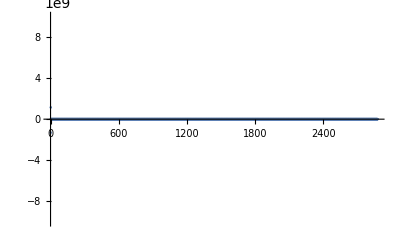

```mathematica
Max[Eigenvalues[H]]
Min[Eigenvalues[H]]
ListPlot[Eigenvalues[H],PlotRange->{-10^10,10^10}]
```

$Aborted

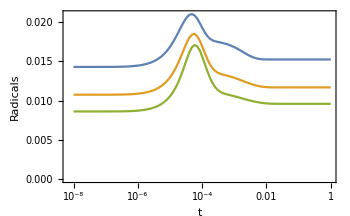

```mathematica
Nt=100;
t0=10.^-8;
t1=1.;
rads={};
Monitor[Do[
filebase="data/h2o2/"<>ToString[n]<>"/";
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
states=Table[pos=First/@Position[evals,u_/;Abs[u*t]<100];((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]]),{t,times}];
radicals=Transpose[{times,Total/@(states.radicalnorm)}];
AppendTo[rads,radicals];,{n,3,9}],n]
ListLogLinearPlot[rads,Axes->False,Frame->True,FrameLabel->{t,"Radicals"},LabelStyle->Directive[Black,16],FrameStyle->Directive[16,Black],ImageSize->350,Joined->True,PlotRange->All]
```

data/h2o2/3/

{376,9,0.135705}

13

3.50888×10^-14

{3.37406,Null}

2.50556×10^8

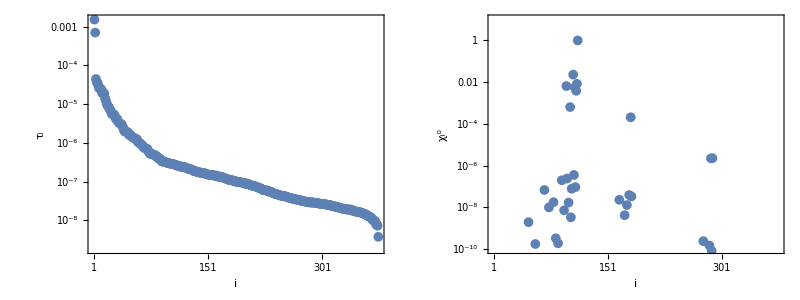

fig3.pdf

0.657416

```mathematica
filebase="data/h2o2/3/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
svals=BinaryReadList[filebase<>"singularvalues.npy","Real64"][[17;;-1]];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
r=1/2;
AbsoluteTiming[angles=ParallelTable[ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}];]
max=Pi/2;
r=1;
cf=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*(Pi/2-#)/max]&;
max2=N[Max[A]]
cf2=Blend[System`PlotThemeDump`$ThemeDefaultMatrix,0.5+0.5*#/max2]&;
p=Grid[{{Show[rasterizeBackground[MatrixPlot[Abs[A],ImageSize->350,AspectRatio->r,ColorFunctionScaling->False,ColorFunction->cf2,FrameTicks->{{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]},{Table[{Round[i],""},{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},FrameLabel->{{None,None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},MaxPlotPoints->200]],Epilog->Inset[BarLegend[{cf2,{0,max2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->DisplayForm[RowBox[{Subsuperscript[W,i,k],"/",HoldForm[10^18]}]]],ImageScaled[{0.55,0.88}]]],Show[rasterizeBackground[MatrixPlot[angles,ImageSize->350,AspectRatio->r,PlotRange->All,FrameTicks->{Table[Round[i],{i,1,Length[evecs],(Length[evecs]-1)/5}],Table[{Round[i],""},{i,1,Length[evecs],(Length[evecs]-1)/5}]},FrameLabel->{{None,
None},{k,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{80,25},{10,85}},DataReversed->{False,False},ColorFunctionScaling->False,ColorFunction->cf]],Epilog->Inset[BarLegend[{cf,{Pi/2-max,Pi/2}},LegendLayout->"Row",LabelStyle->Directive[Black,14],FrameStyle->Directive[Black,AbsoluteThickness[2]], TicksStyle->Directive[Black,AbsoluteThickness[1.5]],LegendLabel->Subsuperscript[θ,i,k]],ImageScaled[{0.55,0.88}]]]},{ListLogPlot[Reverse[-1/Re[evals[[1;;-2]]]],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript[τ,i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImagePadding->{{80,25},{65,10}},ImageSize->350,FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],ListLogPlot[Abs[evecs[[-1]]],PlotRange->{10^-10,10},Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subsuperscript[χ,i,0]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]]}}]
Export["fig3.pdf",p]
Total[Abs[evals]^2]/Total[svals^2]
```

data/h2o2/4/

{1141,9,0.833907}

7

Part::take: Cannot take positions 1141 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

Part::take: Cannot take positions 1140 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

Part::take: Cannot take positions 1139 through 1141 in {{-2.96213×10^-16+0. ⅈ,-1.53714×10^-15+0. ⅈ,-4.17755×10^-16+0. ⅈ,6.48312×10^-17+0. ⅈ,2.1274×10^-15+0. ⅈ,-2.4021×10^-17+0. ⅈ,2.19697×10^-7+0. ⅈ,«37»,-3.56254×10^-16+0. ⅈ,-0.00521046+0. ⅈ,-1.0278×10^-11+0. ⅈ,4.48108×10^-16+0. ⅈ,6.16866×10^-18+0. ⅈ,-6.83508×10^-13+0. ⅈ,«1091»},{«1»},«48»,«550»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

ListLogPlot::lpn: norms is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

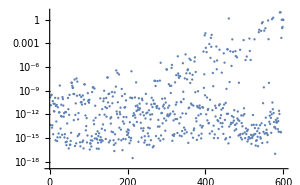
-Graphics- | ListLogPlot[norms,ImageSize→300]

```mathematica
filebase="data/h2o2/4/"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Monitor[norms=Table[vecs=evecs[[dim-n;;dim]];αn=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[vecs];{n,Norm[Normal[SparseArray[{{ind}->1},{dim}]]-αn.vecs]},{n,0,dim-1,1}];,N[n/dim]]
Grid[{{ListLogPlot[Abs[α],PlotRange->All,ImageSize->300],ListLogPlot[norms,ImageSize->300]}}]
```

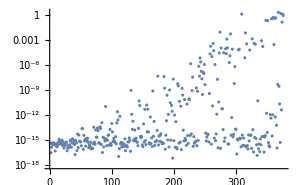

```mathematica
n=dim-1;
vecs=evecs[[dim-n;;dim]];αn=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[vecs];
ListLogPlot[Abs[αn],PlotRange->All,ImageSize->300]
```

### Non - normality measure

data/sweep2/40_35

{2555,9,98.3753}

{0.886293,614.232}

7

{4.94705,Null}

{0.604479,Null}

{0.58579,Null}

{0.882829,Null}

{0.916997,Null}

{0.864376,Null}

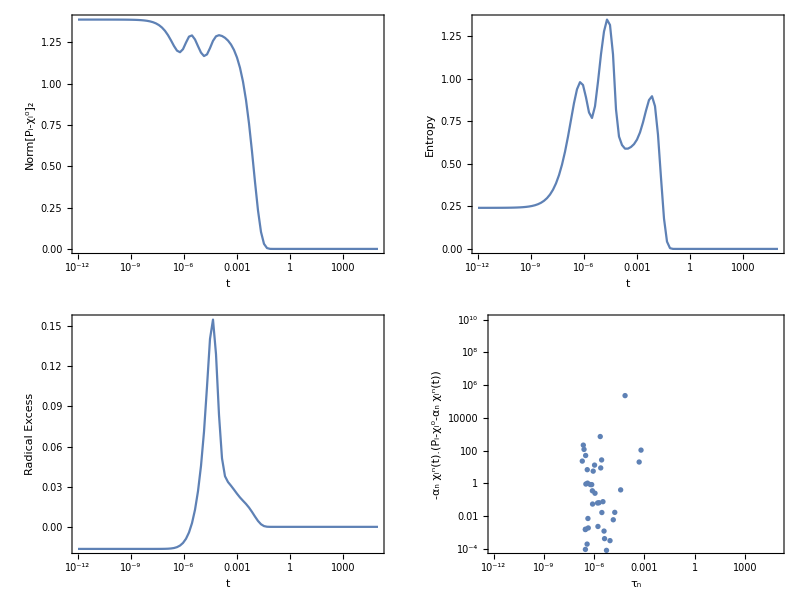

explosive.pdf

```mathematica
filebase="data/sweep2/40_35"
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]]
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
{pressures[[ind]],temperatures[[ind]]}
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0]
AbsoluteTiming[α=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs];]
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]]))&/@multiindices)];

Nt=100;
t0=10.^-12;
t1=10^5.;
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
AbsoluteTiming[states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-3],First/@Position[evals,u_/;Abs[u*t]<100]];Re[((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];]
AbsoluteTiming[projections=Table[t=-1/Re[evals[[i]]];pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{dim,i}];If[pos=={},10^-16,-Re[Conjugate[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])].((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])/Norm[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])]^2]-1],{i,Cases[Range[Length[evals]-1],u_/;Abs[α][[u]]>10^-6]}];]
tau=-1/Re[evals[[Cases[Range[Length[evals]-1],u_/;Abs[α][[u]]>10^-6]]]];
AbsoluteTiming[Pnorm=Norm[#-α[[-1]]*evecs[[-1]],2]&/@states;]
AbsoluteTiming[entropy=Total/@(-Abs[(#-α[[-1]]*evecs[[-1]])]*Log[10^-16+Abs[(#-α[[-1]]*evecs[[-1]])]]&/@states);]
AbsoluteTiming[radicals=Total/@((Re[#-α[[-1]]*evecs[[-1]]]&/@states).radicalnorm);]
file=OpenWrite[filebase<>"times.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[times],"Real64"];
Close[file];
file=OpenWrite[filebase<>"states.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[states],"Real64"];
Close[file];
file=OpenWrite[filebase<>"projections.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[projections],"Real64"];
Close[file];
file=OpenWrite[filebase<>"norms.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[Pnorm],"Real64"];
Close[file];
file=OpenWrite[filebase<>"entropies.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[entropy],"Real64"];
Close[file];
file=OpenWrite[filebase<>"radicals.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[radicals],"Real64"];
Close[file];
file=OpenWrite[filebase<>"taus.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tau],"Real64"];
Close[file];
p=Grid[{{ListLogLinearPlot[Transpose[{times,Pnorm}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t",Subscript[Norm[Subscript[P,i]-Subsuperscript[χ,i,0]],2]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLinearPlot[Transpose[{times,entropy}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]},{ListLogLinearPlot[Transpose[{times,radicals}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Radical Excess"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLogPlot[Transpose[{tau,projections}],Axes->False,Frame->True,FrameLabel->{Subscript[τ,n],HoldForm[-Subscript["α",n]*Subsuperscript[χ,i,n]["t"].(Subscript[P,i]-Subsuperscript[χ,i,0]-Subscript["α",n]*Subsuperscript[χ,i,n]["t"])]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},{10^-4,10^10}},ImageSize->300]}}]
Export["explosive.pdf",p]
```

```mathematica
Monitor[Do[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
α=Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs];
radicalnorm=SparseArray[({#,#}&/@Range[dim])->(((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices)];
Nt=100;
t0=10.^-10;
t1=10^5;
times=Table[t0*(t1/t0)^(i/Nt),{i,0,Nt}];
states=Table[pos=Intersection[First/@Position[α,u_/;Abs[u]>10^-3],First/@Position[evals,u_/;Abs[u*t]<100]];Re[((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])],{t,times}];
projections=Table[t=-1/Re[evals[[i]]];pos=Complement[Intersection[First/@Position[α,u_/;Abs[u]>10^-6],First/@Position[evals,u_/;Abs[u*t]<100]],{dim,i}];If[pos=={},10^-16,-Re[Conjugate[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])].((Exp[evals[[pos]]*t]*α[[pos]]).evecs[[pos]])/Norm[((Exp[evals[[i]]*t]*α[[i]])*evecs[[i]])]^2]],{i,Cases[Range[dim-1],u_/;Abs[α][[u]]>10^-6]}];
tau=-1/Re[evals[[Cases[Range[dim-1],u_/;Abs[α][[u]]>10^-6]]]];
Pnorm=Norm[#-α[[-1]]*evecs[[-1]],2]&/@states;
entropy=Total/@(-Abs[(#-α[[-1]]*evecs[[-1]])]*Log[10^-16+Abs[(#-α[[-1]]*evecs[[-1]])]]&/@states);
radicals=Total/@((Re[#-α[[-1]]*evecs[[-1]]]&/@states).radicalnorm);
file=OpenWrite[filebase<>"times.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[times],"Real64"];
Close[file];
file=OpenWrite[filebase<>"states.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[states],"Real64"];
Close[file];
file=OpenWrite[filebase<>"projections.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[projections],"Real64"];
Close[file];
file=OpenWrite[filebase<>"norms.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[Pnorm],"Real64"];
Close[file];
file=OpenWrite[filebase<>"entropies.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[entropy],"Real64"];
Close[file];
file=OpenWrite[filebase<>"radicals.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[radicals],"Real64"];
Close[file];
file=OpenWrite[filebase<>"taus.dat",BinaryFormat->True];
BinaryWrite[file,Flatten[tau],"Real64"];
Close[file];,{n,0,50},{m,0,50}];,{m,n}]
```

```mathematica
Monitor[test=Table[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Real64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
{dim,ns,runtime} = dat[[1]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evals[[-1]]=0;
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
{temperatures[[ind]],pressures[[ind]], Total[Abs[evals]^2]/Total[Total[A^2]],Max@Eigenvalues[1/2*(A+Transpose[A])]},{n,0,50},{m,0,50}];,{temperatures[[ind]],pressures[[ind]], Total[Abs[evals]^2]/Total[Total[A^2]],Max@Eigenvalues[1/2*(A+Transpose[A])]}]
```

Eigenvalues::arh: Because finding 1344 out of the 1344 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

$Aborted

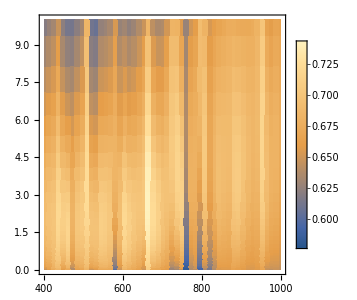
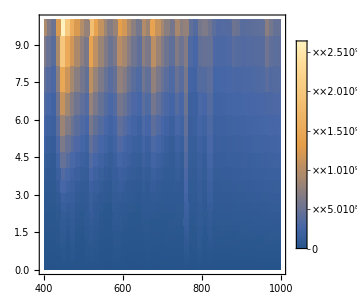
-Graphics- | -Graphics-

```mathematica
Grid[{{ListDensityPlot[Flatten[test,1][[All,{1,2,3}]],PlotLegends->True,InterpolationOrder->0,ImageSize->300],ListDensityPlot[Flatten[test,1][[All,{1,2,4}]],PlotLegends->True,InterpolationOrder->0,ImageSize->300,PlotRange->All]}}]
```

```mathematica
Manipulate[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];times=BinaryReadList[filebase<>"times.dat", "Real64"];states=BinaryReadList[filebase<>"states.dat", "Real64"];projections=BinaryReadList[filebase<>"projections.dat", "Real64"];Pnorm=BinaryReadList[filebase<>"norms.dat", "Real64"];entropy=BinaryReadList[filebase<>"entropies.dat", "Real64"];
radicals=BinaryReadList[filebase<>"radicals.dat", "Real64"];tau=BinaryReadList[filebase<>"taus.dat", "Real64"];
Grid[{{ListLogLinearPlot[Transpose[{times,Pnorm/2^(1/2)}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t",Subscript[Norm[Subscript[P,i]-Subsuperscript[χ,i,0]],2]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLinearPlot[Transpose[{times,entropy}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]},{ListLogLinearPlot[Transpose[{times,radicals}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Radical Excess"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLogPlot[Transpose[{tau,projections}],Axes->False,Frame->True,FrameLabel->{Subscript[τ,"n"],HoldForm[-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]].(Subscript[P,i]-Subsuperscript[χ,i,0]-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]])]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},{10^-10,10^10}},ImageSize->300]}}],{n,0,50,1},{m,0,50,1}]
```

```mathematica
Monitor[sweep=Table[filebase="data/sweep/"<>ToString[n]<>"_"<>ToString[m];
dat=Import[filebase<>"out.dat"];
{dim,ns,runtime} = dat[[1]];times=BinaryReadList[filebase<>"times.dat", "Real64"];states=BinaryReadList[filebase<>"states.dat", "Real64"];projections=BinaryReadList[filebase<>"projections.dat", "Real64"];Pnorm=BinaryReadList[filebase<>"norms.dat", "Real64"];entropy=BinaryReadList[filebase<>"entropies.dat", "Real64"];
radicals=BinaryReadList[filebase<>"radicals.dat", "Real64"];tau=BinaryReadList[filebase<>"taus.dat", "Real64"];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],ns];
ind=First@FirstPosition[multiindices,u_/;Length[u]>0&&u[[2]]==0&&u[[3]]==0&&u[[6]]==0&&u[[7]]==0&&u[[8]]==0];
{temperatures[[ind]],pressures[[ind]], times,Pnorm,entropy,radicals,tau,projections},{m,0,50},{n,0,50}];,{m,n}]
```

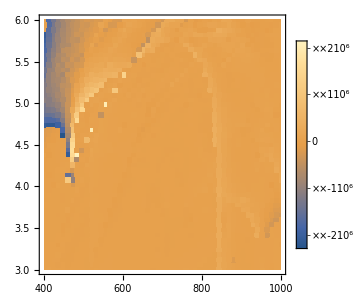
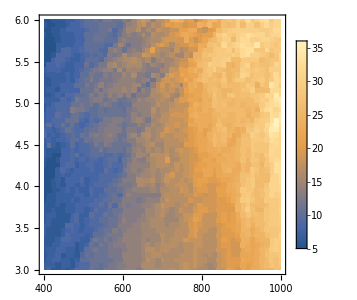
-Graphics- | -Graphics-

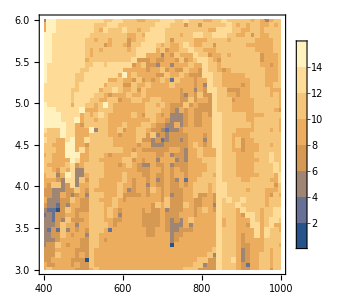
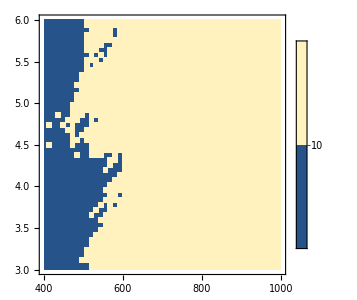
-Graphics- | -Graphics-

```mathematica
Grid[{{ListDensityPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Total[#[[8]]]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300],
ListDensityPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Count[#[[8]],u_/;u>0]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300]}}]
Grid[{{ListContourPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Log[Abs[Total[#[[8]]]]]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300],
ListContourPlot[{#[[1]],Log[#[[2]]*10^5]/Log[10],Count[#[[8]],u_/;u>0]}&/@Flatten[sweep,1],PlotRange->All,InterpolationOrder->0,PlotLegends->True,ImageSize->300,Contours->{10}]}}]
```

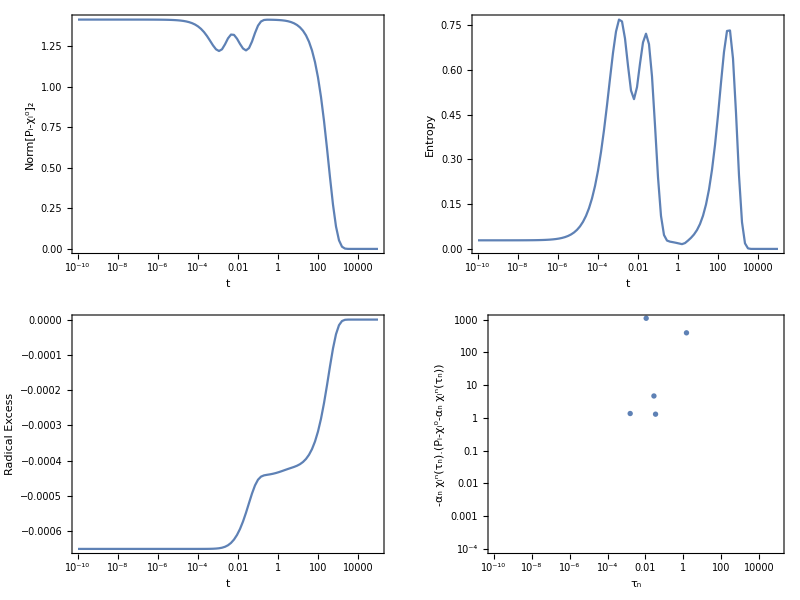

```mathematica
n=1;
m=1;
Grid[{{ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,4]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t",Subscript[Norm[Subscript[P,i]-Subsuperscript[χ,i,0]],2]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,5]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Entropy"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300]},{ListLogLinearPlot[Transpose[{sweep[[n,m,3]],sweep[[n,m,6]]}],Joined->True,Axes->False,Frame->True,FrameLabel->{"t","Radical Excess"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},All},ImageSize->300],ListLogLogPlot[Transpose[{sweep[[n,m,7]],sweep[[n,m,8]]}],Axes->False,Frame->True,FrameLabel->{Subscript[τ,"n"],HoldForm[-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]].(Subscript[P,i]-Subsuperscript[χ,i,0]-Subscript["α","n"]*Subsuperscript[χ,i,"n"][Subscript[τ,"n"]])]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{{t0,t1},{10^-4,1000}},ImageSize->300]}}]
```

## Concentration evolutions

data/h2o2/

{417.349,Null}

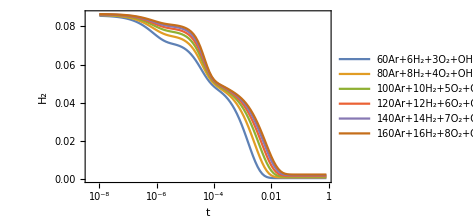
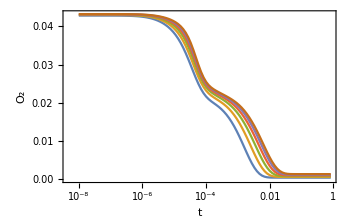
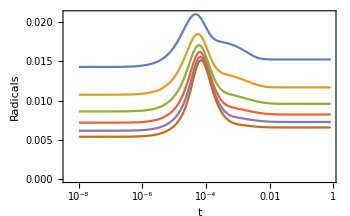
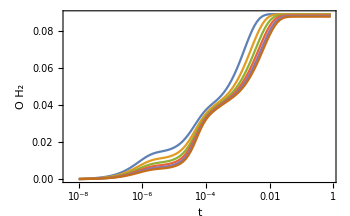
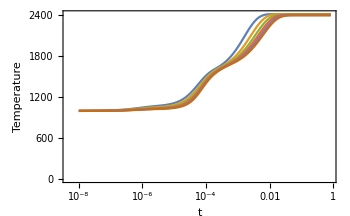
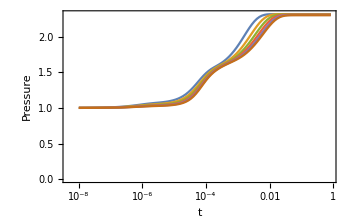

```mathematica
o2dats={};
h2dats={};
h2odats={};
radicaldats={};
temperaturedats={};
pressuredats={};
initials={};
filebase0="data/h2o2/"
AbsoluteTiming[Monitor[Do[filebase=filebase0<>ToString[m]<>"/";
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
ind=1;
initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{ToString[#[[2]]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[Table[{multiindices[[i]],spforms},{i,1,dim}][[ind]]],Null]];
AppendTo[initials,initial];
states=Partition[BinaryReadList[filebase<>"propogate.npy","Real64"][[17;;-1]],dim];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
(*Abs[(Total[#]-Total[evecs[[-1]].h2norm]/Total[evecs[[-1]]])]*)
AppendTo[h2dats,Transpose[{times,Total[#]&/@(states.h2norm)}]];
AppendTo[o2dats,Transpose[{times,Total[#]&/@(states.o2norm)}]];
AppendTo[radicaldats,Transpose[{times,Total[#]&/@(states.radicalnorm)}]];
AppendTo[h2odats,Transpose[{times,Total[#]&/@(states.h2onorm)}]];
AppendTo[temperaturedats,Transpose[{times,Total[#]&/@(states.temperaturenorm)}]];
AppendTo[pressuredats,Transpose[{times,Total[#]&/@(states.pressurenorm)}]];
p=Legended[ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]];,{m,3,8}],{m,n, p}]]
p=Legended[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}},Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]]
```

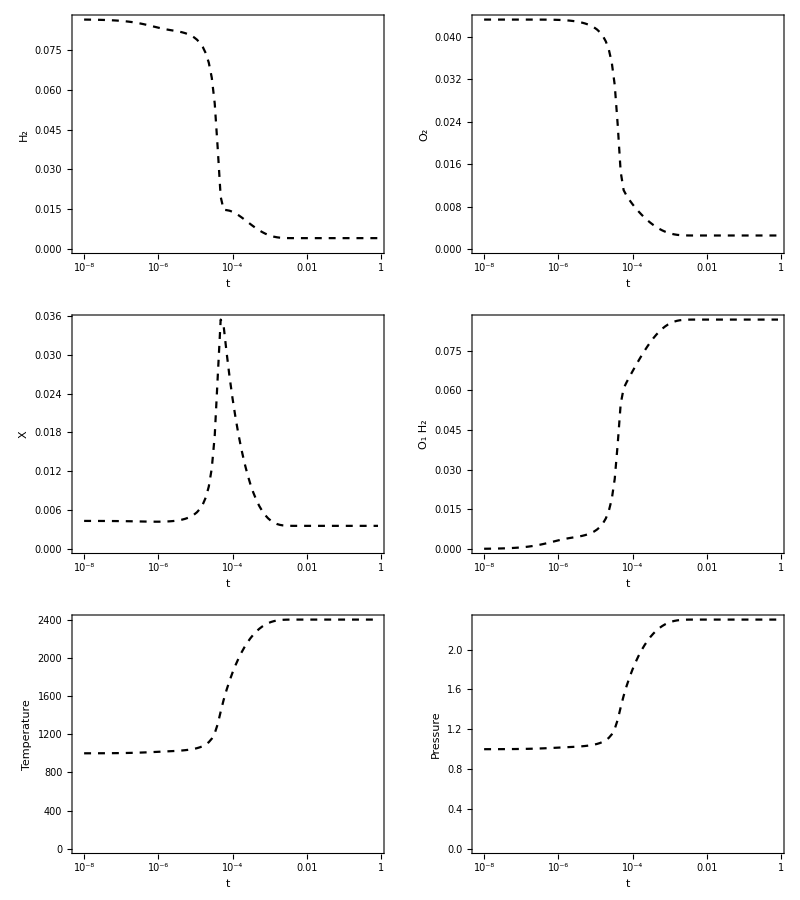

```mathematica
dat=Import["data/h2o2.csv"];
{{p0,p1},{p2,p3},{p4,p5}}={{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,7]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,5]]+dat[[2;;-1,6]]+dat[[2;;-1,8]]+dat[[2;;-1,10]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,9]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,2]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,3]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]}};
Grid[{{p0,p1},{p2,p3},{p4,p5}}]
```

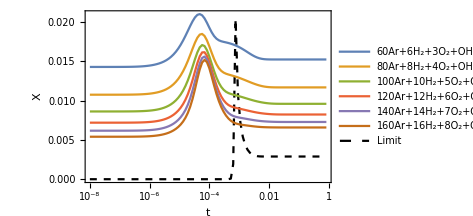

```mathematica
p=Legended[Show[p2,ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,X},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],PlotRange->All],Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]
```

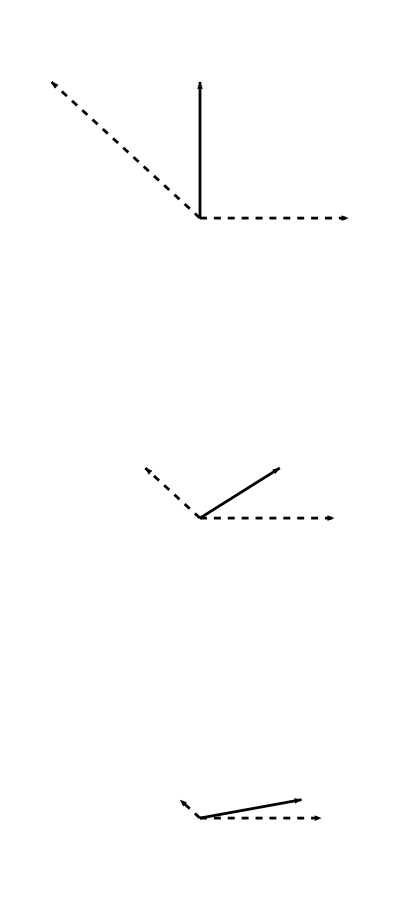

```mathematica
ϵ=0.25;
x1[t_]:=Exp[-t]*{1,0}
x2[t_]:=Exp[-10*t]*{-1,ϵ}
x[t_]:=x1[t]+x2[t]
p0=Grid@Transpose[{Table[Graphics[{AbsoluteThickness[2],Arrowheads[0.07],Arrow[{{0,0},x[t]}],Dashed, Arrow[{{0,0},x1[t]}],Arrow[{{0,0},x2[t]}]},PlotRange->{{-1.1,1.1},{-0.1,ϵ+0.1}},ImageSize->250],{t,0,0.2,0.1}]}]
```

data/h2o2/3/

{18,376,1.3744,12639,10}

4.46967×10^-15

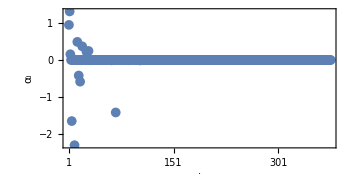
-Graphics- | -Graphics-
-Graphics-

fig2.pdf

```mathematica
filebase="data/h2o2/3/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
ind=1;
α=Re[Normal[SparseArray[{{ind}->1},{dim}]].PseudoInverse[evecs]];
Norm[Re[α.evecs-Normal[SparseArray[{{ind}->1},{dim}]]]]
p=Grid[{{Grid[{{ListPlot[Reverse[α],PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{i,Subscript["α",i]},LabelStyle->Directive[16,Black],AspectRatio->r,ImageSize->350,ImagePadding->{{80,25},{65,10}},FrameTicks->{{Automatic,Automatic},{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[{Round[i],""},{i,1,dim,(dim-1)/5}]}},PlotStyle->Directive[PointSize[0.02]]],p0}}]},{p}}]
Export["fig2.pdf",p]
```

## Runtimes

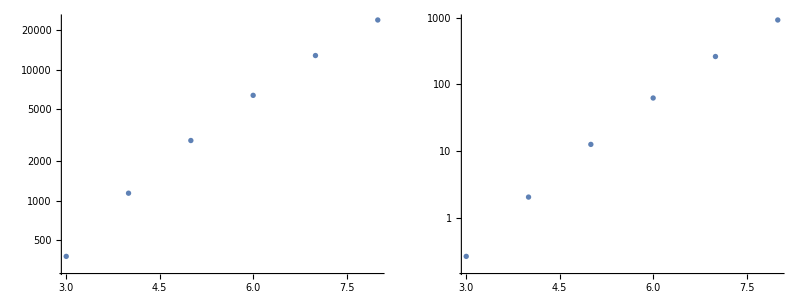

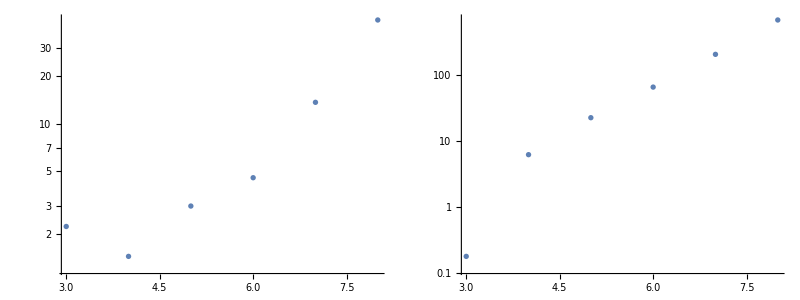

```mathematica
Grid[{{ListLogPlot[Import["statesruntime.dat"][[All,{1,2}]],ImageSize->300],ListLogPlot[Import["statesruntime.dat"][[All,{1,3}]],ImageSize->300]}}]
Grid[{{ListLogPlot[Import["calculateruntime.dat"][[All,{1,2}]],ImageSize->300],ListLogPlot[Import["eigenvaluesruntime.dat"][[All,{1,2}]],ImageSize->300]}}]
```

```mathematica
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["statesruntime.dat"][[All,{1,3}]][[2;;-1]],{1,x},x]
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["calculateruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["eigenvaluesruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]

Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["statesruntime.dat"][[All,{1,3}]][[2;;-1]],{1,x},x]*1/3600/.x->10
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["calculateruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]*1/3600/.x->10
Exp[#/.x->0]*Exp[D[#,x]]^x&@Fit[{#[[1]],Log[#[[2]]]}&/@Import["eigenvaluesruntime.dat"][[All,{1,2}]][[2;;-1]],{1,x},x]*1/3600/.x->12
```

0.00563486 4.58589^x

0.0422938 2.31821^x

0.0628461 3.18854^x

6.43894

0.0526626

19.2788

## Kmatrix

data/grimech

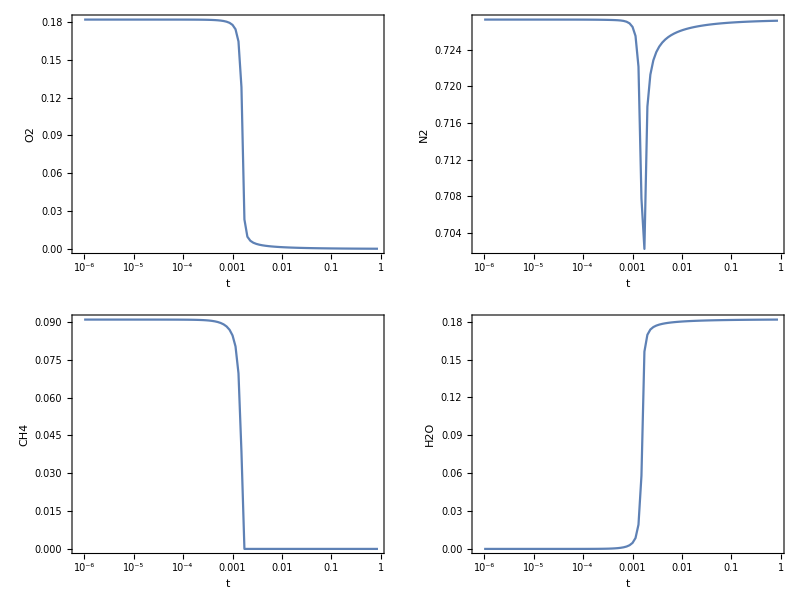

```mathematica
filebase="data/grimech"
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
Nt=Length[times];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],Length[times]];
ns=Length[evals];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],ns]];
Grid[{{ListLogLinearPlot[Transpose[{times,concentrations[[4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"O2"}],
ListLogLinearPlot[Transpose[{times,concentrations[[48]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"N2"}]},
{ListLogLinearPlot[Transpose[{times,concentrations[[14]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"CH4"}],
ListLogLinearPlot[Transpose[{times,concentrations[[6]]}],PlotRange->All,Joined->True, Axes->False,Frame->True,LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,FrameLabel->{t,"H2O"}]}}]
```

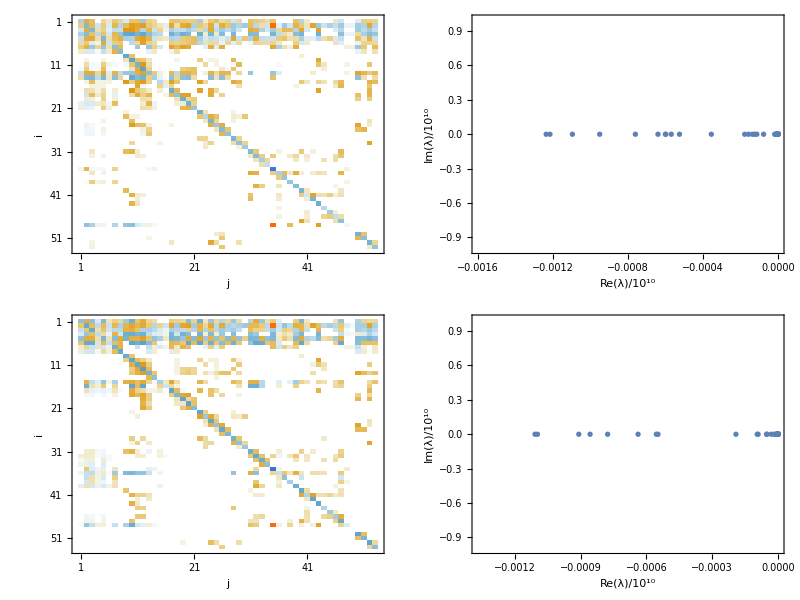

```mathematica
matrices=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
p=Grid[{{MatrixPlot[matrices[[1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices[[1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]},{MatrixPlot[matrices[[-1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices[[-1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]}}]
```

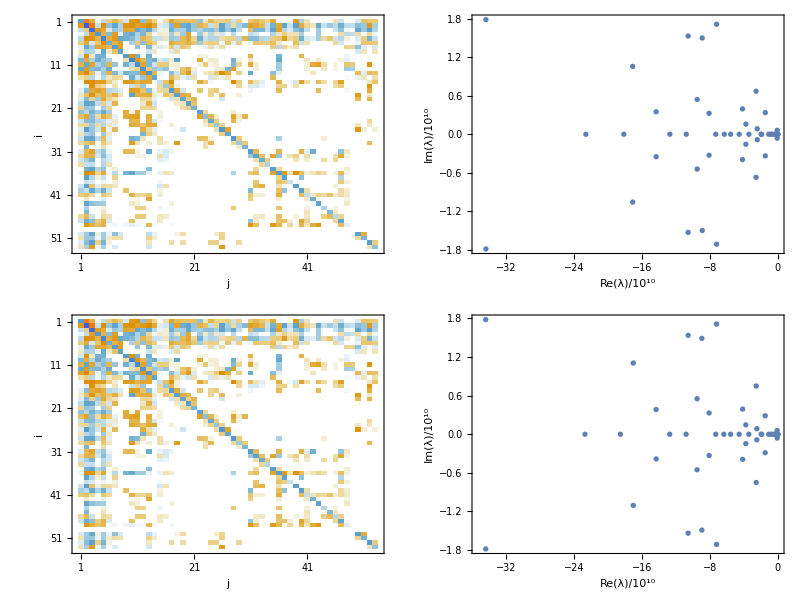

```mathematica
matrices2=Partition[Partition[BinaryReadList[filebase<>"matrices2.npy","Real64"][[17;;-1]],ns],ns];
p=Grid[{{MatrixPlot[matrices2[[1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices2[[1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]},{MatrixPlot[matrices2[[-1]],FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],FrameLabel->{i,j},ImageSize->350,FrameTicks->{{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]},{Table[i,{i,1,51,10}],Table[{i,""},{i,1,51,10}]}},ImagePadding->{{75,10},{75,10}}],ListPlot[{Re[#]/10^10,Im[#]/10^10}&/@Eigenvalues[matrices2[[-1]]],Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Re[λ],"/",HoldForm[10^10]}]],DisplayForm[RowBox[{Im[λ],"/",HoldForm[10^10]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],AspectRatio->1,ImageSize->350,ImagePadding->{{75,10},{75,10}}]}}]
```